```mathematica
θ=0;
```

```mathematica
Solve[mx^2*(2*v1^2-mn/mx*v2prime^2-2*v1*(v1^2-mn/mx*v2prime^2)^0.5*Cos[θ])==mn^2*v2prime^2,v2prime]
```

{{v2prime→0.},{v2prime→-(2. mx v1)/(√(mn^2+2. mn mx+mx^2))},{v2prime→(2. mx v1)/(√(mn^2+2. mn mx+mx^2))}}

```mathematica
Solve[mx^2*(2*v1^2-mn/mx*v2prime^2+2*v1*(v1^2-mn/mx*v2prime^2)^0.5*Cos[θ])==mn^2*v2prime^2,v2prime]
```

{{v2prime→0.},{v2prime→-(2. mx v1)/(√(mn^2+2. mn mx+mx^2))},{v2prime→(2. mx v1)/(√(mn^2+2. mn mx+mx^2))}}

```mathematica
NIntegrate[Exp[-x^2],{x,0,1}]
```

0.746824

```mathematica
Series[1-(1-Exp[-a^2])/a^2,{a,0,2}]
```

a^2/2+O[a]^3

```mathematica
Series[(0.5*(a+η)*Exp[-(a-η)^2]-0.5*(a-η)*Exp[-(a+η)^2]-η*Exp[-η^2])/(2*η*a^2),{a,0,2}]
```

1. ⅇ^(-η^2) (0.5+1. η^2)+0.333333 ⅇ^(-η^2) (-2.25-1. η^2+1. η^4) a^2+O[a]^3

```mathematica
(*THERMAL SCATTERING*)
```

```mathematica
s=((vn^2+μ^2*w^2+2*μ*vn*w*z)^0.5)/(1+μ);
t=((vn^2+w^2-2*vn*w*z)^0.5)/(1+μ);
a=D[s,vn]
```

(0.5 (2 vn+2 w z μ))/((1+μ) (vn^2+2 vn w z μ+w^2 μ^2)^0.5)

```mathematica
b=D[s,z]
```

(1. vn w μ)/((1+μ) (vn^2+2 vn w z μ+w^2 μ^2)^0.5)

```mathematica
c=D[t,z]
```

-(1. vn w)/((vn^2+w^2-2 vn w z)^0.5 (1+μ))

```mathematica
d=D[t,vn]
```

(0.5 (2 vn-2 w z))/((vn^2+w^2-2 vn w z)^0.5 (1+μ))

```mathematica
FullSimplify[(a*c-b*d)]
```

-(1. vn^2 w)/((vn^2+w^2-2 vn w z)^0.5 (1.+1. μ) (vn^2+2 vn w z μ+w^2 μ^2)^0.5)

```mathematica
FullSimplify[(2*μ*(μ+1)/2*t^2+2*(μ+1)/2*s^2-μ*w^2)]
```

((vn^2+w^2-2 vn w z)^1. μ-w^2 μ (1+μ)+(vn^2+2 vn w z μ+w^2 μ^2)^1.)/(1+μ)

```mathematica
FullSimplify[((μ+1)/2*(s+t)+(μ-1)/2*(t-s))^2+μ*((t-s)^2-w^2)]
```

((vn^2+w^2-2 vn w z)^1. μ-w^2 μ (1+μ)+(vn^2+2 vn w z μ+w^2 μ^2)^1.)/(1+μ)

```mathematica
FullSimplify[((μ+1)/2*(t-s)+(μ-1)/2*(t+s))^2+μ*((t+s)^2-w^2)]
```

((vn^2+w^2-2 vn w z)^1. μ-w^2 μ (1+μ)+(vn^2+2 vn w z μ+w^2 μ^2)^1.)/(1+μ)

```mathematica
s=(μ*w)/(1+μ);
t=w/(1+μ);
```

```mathematica
FullSimplify[2*mχ^2*t^2*(1-((s^2+t^2-v^2)*(s^2+t^2-w^2))/(4*s^2*t^2))]
```

(mχ^2 (-v^2+w^2))/μ

```mathematica
Integrate[x*Exp[-k^2*x^2],{x,x1,x2}]
```

(ⅇ^(-k^2 x1^2)-ⅇ^(-k^2 x2^2))/(2 k^2)

```mathematica
κ=m/(2*T);
μplus=(μ+1)/2;
μminus=(μ-1)/2;
αplus=κ*(μplus*v+μminus*w);
αminus=κ*(μplus*v-μminus*w);
βplus=κ*(μminus*v+μplus*w);
βminus=κ*(μminus*v-μplus*w);
χ[a_,b_]:=Integrate[Exp[-y^2],{y,a,b}];
```

```mathematica
a=FullSimplify[2*κ^2*μplus^2*Integrate[v*χ[αminus,αplus],v]]
```

1/(32 T^2)ⅇ^(-(m^2 ((v-w)^2+2 v^2 μ+(v+w)^2 μ^2))/(16 T^2)) (ⅇ^((m^2 ((v-w)^2+2 v^2 μ+(v+w)^2 μ^2))/(16 T^2)) √π (8 T^2-m^2 (v+w+v μ-w μ) (v-w+(v+w) μ)) (Erf[(m (v+w+v μ-w μ))/(4 T)]-Erf[(m (v-w+(v+w) μ))/(4 T)])+8 ⅇ^((m^2 w (w μ+v (-1+μ^2)))/(8 T^2)) m T (-w (-1+μ) Cosh[(m^2 v w (-1+μ^2))/(8 T^2)]-v (1+μ) Sinh[(m^2 v w (-1+μ^2))/(8 T^2)]))

```mathematica
b=FullSimplify[1/2*αminus*Exp[-αplus^2]-1/2*αplus*Exp[-αminus^2]+(αplus*αminus-1/2)*χ[αminus,αplus]]
```

1/(8 T^2)(ⅇ^(-(m^2 (v-w+(v+w) μ)^2)/(16 T^2)) m T (v+w+v μ-w μ)-ⅇ^(-(m^2 (v+w+v μ-w μ)^2)/(16 T^2)) m T (v-w+(v+w) μ)+1/4 √π (8 T^2-m^2 (v+w+v μ-w μ) (v-w+(v+w) μ)) (Erf[(m (v+w+v μ-w μ))/(4 T)]-Erf[(m (v-w+(v+w) μ))/(4 T)]))

```mathematica
FullSimplify[a-b]
```

0

```mathematica
c=FullSimplify[2*κ^2*μplus^2*Integrate[v*χ[-αminus,αplus],v]]
```

1/(32 T^2)ⅇ^(-(m^2 ((v-w)^2+2 v^2 μ+(v+w)^2 μ^2))/(16 T^2)) (-ⅇ^((m^2 ((v-w)^2+2 v^2 μ+(v+w)^2 μ^2))/(16 T^2)) √π (8 T^2-m^2 (v+w+v μ-w μ) (v-w+(v+w) μ)) (Erf[(m (v+w+v μ-w μ))/(4 T)]+Erf[(m (v-w+(v+w) μ))/(4 T)])+8 ⅇ^((m^2 w (w μ+v (-1+μ^2)))/(8 T^2)) m T (v (1+μ) Cosh[(m^2 v w (-1+μ^2))/(8 T^2)]+w (-1+μ) Sinh[(m^2 v w (-1+μ^2))/(8 T^2)]))

```mathematica
d=FullSimplify[1/2*αminus*Exp[-αplus^2]+1/2*αplus*Exp[-αminus^2]+(αplus*αminus-1/2)*χ[-αminus,αplus]]
```

1/(32 T^2)(4 ⅇ^(-(m^2 (v-w+(v+w) μ)^2)/(16 T^2)) m T (v+w+v μ-w μ)+4 ⅇ^(-(m^2 (v+w+v μ-w μ)^2)/(16 T^2)) m T (v-w+(v+w) μ)-√π (8 T^2-m^2 (v+w+v μ-w μ) (v-w+(v+w) μ)) (Erf[(m (v+w+v μ-w μ))/(4 T)]+Erf[(m (v-w+(v+w) μ))/(4 T)]))

```mathematica
FullSimplify[c-d]
```

0

```mathematica
e=FullSimplify[2*κ^2*μplus^2*Integrate[w*χ[βminus,βplus],w]]
```

1/(32 T^2)ⅇ^(-(m^2 ((v-w)^2+2 w^2 μ+(v+w)^2 μ^2))/(16 T^2)) (-ⅇ^((m^2 ((v-w)^2+2 w^2 μ+(v+w)^2 μ^2))/(16 T^2)) √π (8 T^2+m^2 (-v+w+(v+w) μ) (v (-1+μ)-w (1+μ))) (Erf[(m (v+w-v μ+w μ))/(4 T)]+Erf[(m (-v+w+(v+w) μ))/(4 T)])+8 ⅇ^((m^2 v (v μ+w (-1+μ^2)))/(8 T^2)) m T (w (1+μ) Cosh[(m^2 v w (-1+μ^2))/(8 T^2)]+v (-1+μ) Sinh[(m^2 v w (-1+μ^2))/(8 T^2)]))

```mathematica
f=FullSimplify[-1/2*βminus*Exp[-βplus^2]+1/2*βplus*Exp[-βminus^2]+(-βplus*βminus-1/2)*χ[βminus,βplus]]
```

(ⅇ^(-(m^2 (-v+w+(v+w) μ)^2)/(16 T^2)) m T (v+w-v μ+w μ)+ⅇ^(-(m^2 (v+w-v μ+w μ)^2)/(16 T^2)) m T (-v+w+(v+w) μ)-1/4 √π (8 T^2+m^2 (v^2 (-1+μ)^2-w^2 (1+μ)^2)) (Erf[(m (v+w-v μ+w μ))/(4 T)]+Erf[(m (-v+w+(v+w) μ))/(4 T)]))/(8 T^2)

```mathematica
FullSimplify[e-f]
```

0

```mathematica
g=FullSimplify[2*κ^2*μplus^2*Integrate[w*χ[-βminus,βplus],w]]
```

1/(32 T^2)ⅇ^(-(m^2 ((v-w)^2+2 w^2 μ+(v+w)^2 μ^2))/(16 T^2)) (ⅇ^((m^2 ((v-w)^2+2 w^2 μ+(v+w)^2 μ^2))/(16 T^2)) √π (8 T^2+m^2 (-v+w+(v+w) μ) (v (-1+μ)-w (1+μ))) (Erf[(m (v+w-v μ+w μ))/(4 T)]-Erf[(m (-v+w+(v+w) μ))/(4 T)])-8 ⅇ^((m^2 v (v μ+w (-1+μ^2)))/(8 T^2)) m T (v (-1+μ) Cosh[(m^2 v w (-1+μ^2))/(8 T^2)]+w (1+μ) Sinh[(m^2 v w (-1+μ^2))/(8 T^2)]))

```mathematica
h=FullSimplify[-1/2*βminus*Exp[-βplus^2]-1/2*βplus*Exp[-βminus^2]+(-βplus*βminus-1/2)*χ[-βminus,βplus]]
```

1/(8 T^2)(ⅇ^(-(m^2 (-v+w+(v+w) μ)^2)/(16 T^2)) m T (v+w-v μ+w μ)-ⅇ^(-(m^2 (v+w-v μ+w μ)^2)/(16 T^2)) m T (-v+w+(v+w) μ)-1/4 √π (8 T^2+m^2 (v^2 (-1+μ)^2-w^2 (1+μ)^2)) (-Erf[(m (v+w-v μ+w μ))/(4 T)]+Erf[(m (-v+w+(v+w) μ))/(4 T)]))

```mathematica
FullSimplify[g-h]
```

0

```mathematica
(*Integrate[v*Exp[-μ*κ^2*(v^2-w^2)],v]*)
```

-(ⅇ^(-(v^2-w^2) κ^2 μ))/(2 κ^2 μ)

```mathematica
(*Integrate[x*Exp[-x^2]*(a^2-x^2),{x,0,a}]*)
```

1/2 (-1+a^2+ⅇ^(-a^2))

```mathematica
(*MOTION OF THE SHELL WITH DIMENSIONLESS VELOCITY η*) 



aplus=a+η;
aminus=a-η;
χ[p_,q_]:=Integrate[Exp[-y^2],{y,p,q}];
Series[(((aplus*aminus)-0.5)*(χ[-η,η]-χ[a-η,a+η])+0.5*aplus*Exp[-aminus^2]-0.5*aminus*Exp[-aplus^2]-η*Exp[-η^2])/(2*η*a^2*(1-(1-Exp[-a^2])/a^2)),{a,0,3}]
```

1. ⅇ^(-η^2)+0.222222 ⅇ^(-η^2) (-2.498×10^-16+1. η^2) a^2+O[a]^4

```mathematica
a1=Integrate[2*x*Exp[-x^2]*(1-x^2/a^2)*Exp[-η^2]*Sinh[2*x*η]/(2*x*η),{x,0,a}]
```

(-(4 ⅇ^(-η^2) η+2 ⅇ^(-(a+η)^2) (a-η-ⅇ^(4 a η) (a+η))+2 √π (1+2 η^2) Erf[η]+√π (1+2 η^2) (Erf[a-η]-Erf[a+η]))/a^2+2 √π (Erf[a-η]+2 Erf[η]-Erf[a+η]))/(8 η)

```mathematica
a2=(((aplus*aminus)-0.5)*(χ[-η,η]-χ[a-η,a+η])+0.5*aplus*Exp[-aminus^2]-0.5*aminus*Exp[-aplus^2]-η*Exp[-η^2])/(2*η*a^2)
```

(-0.5 ⅇ^(-(a+η)^2) (a-η)-ⅇ^(-η^2) η+0.5 ⅇ^(-(a-η)^2) (a+η)+(-0.5+(a-η) (a+η)) (√π Erf[η]-1/2 √π (-Erf[a-η]+Erf[a+η])))/(2 a^2 η)

```mathematica
FullSimplify[a1-a2]
```

0.

```mathematica
(*MULTISCATTER CAPTURE*)

p1=2*Integrate[(y*Exp[-y*τ]*(y*τ))/1,{y,0,1}]
```

(2 (2-ⅇ^-τ (2+2 τ+τ^2)))/τ^2

```mathematica
Series[(2 (2-ⅇ^-τ (2+2 τ+τ^2)))/τ^2,{τ,0,2}]
```

(2 τ)/3-τ^2/2+O[τ]^3

```mathematica
Integrate[Exp[(-3*(w^2-ve^2))/(2*vbar^2)]*w^3,{w,ve,vn}]
```

1/9 vbar^2 (2 vbar^2+3 ve^2-ⅇ^((3 (ve-vn) (ve+vn))/(2 vbar^2)) (2 vbar^2+3 vn^2))

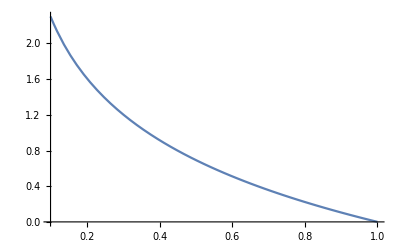

```mathematica
Plot[Log[1/ϵ],{ϵ,0.1,1}]
```

```mathematica
(*MULTIPLE CAPTURE FOR SOLAR MASS WHITE DWARF*)


R=0.01*6.95*10^8(*radius  in m*);
M=2*10^30 (*mass  in kg*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
```

```mathematica
kb=1.38*10^-23;(*in J/K*)
T=10^5;(*in K*)
```

```mathematica
mn=10;(*in Gev*)
```

```mathematica
mx1=10^4;mx2=10^5;mx3=10^6;mx4=10^7;mx5=10^8;(*in Gev*)
```

```mathematica
βplus[mx_]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
vesc=1/1000*((2*G*M)/R)^0.5;(*in km/sec*)
```

```mathematica
ϵ=10^-6;
```

```mathematica
mevap=(3*kb*T)/((vesc*10^3)^2)*5.62*10^26(*in Gev*)
```

0.0000606088

```mathematica
n[u_,mx_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/(1-βplus[mx])]/βplus[mx]];
nbra[u_,mx_]:=Log[vesc^2/(u^2+vesc^2)]/Log[1-βplus[mx]/2];
nself[u_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/ϵ]];
```

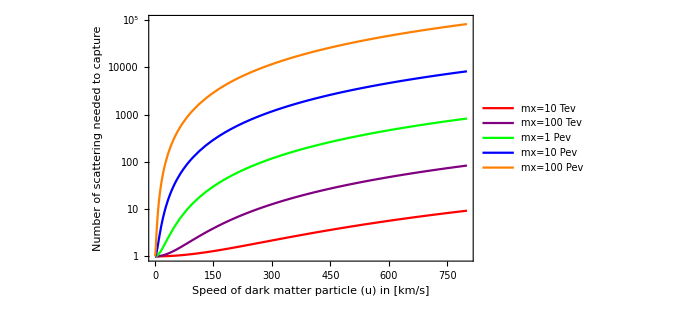

```mathematica
plot1=LogPlot[{n[u,mx1],n[u,mx2],n[u,mx3],n[u,mx4],n[u,mx5]},{u,0,800},PlotRange->{1,10^5},PlotStyle->{Red,Purple,Green,Blue,Orange},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}]
```

```mathematica
plot2=LogPlot[{nbra[u,mx1],nbra[u,mx2],nbra[u,mx3],nbra[u,mx4],nbra[u,mx5]},{u,0,800},PlotRange->{1,10^5},PlotStyle->{Directive[Red,Dashed],Directive[Purple,Dashed],Directive[Green,Dashed],Directive[Blue,Dashed],Directive[Orange,Dashed]},Frame->True,FrameLabel->{Style["Speed of dark matter particle at infinity in [km/s] ",FontSize->20],Style["Maximum  number of scattering",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}];
```

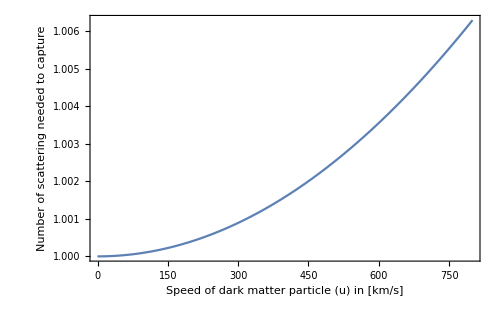

```mathematica
Plot[{nself[u]},{u,0,800},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

```mathematica
(*MULTIPLE CAPTURE FOR SOLAR MASS NEUTRON STAR*)
```

```mathematica
R=10^4(*radius  in m*);
M=2*10^30 (*mass  in kg*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
kb=1.38*10^-23;(*in J/K*)
```

```mathematica
T=10^10;(*in K*)
```

```mathematica
mx1=10^4;mx2=10^5;mx3=10^6;mx4=10^7;mx5=10^8;(*in Gev*)
```

```mathematica
mn=1;(*in Gev*)
```

```mathematica
βplus[mx_]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
vesc=1/1000*((2*G*M)/R)^0.5;(*in km/sec*)
```

```mathematica
ϵ=10^-4;
```

```mathematica
mevap=(3*kb*T)/((vesc*10^3)^2)*5.62*10^26(*in Gev*)
```

0.00872069

```mathematica
n[u_,mx_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/(1-βplus[mx])]/βplus[mx]];
nbra[u_,mx_]:=Log[vesc^2/(u^2+vesc^2)]/Log[1-βplus[mx]/2];
nself[u_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/ϵ]];
```

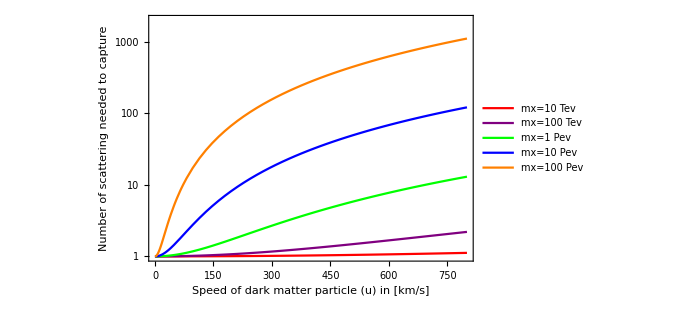

```mathematica
plot1=LogPlot[{n[u,mx1],n[u,mx2],n[u,mx3],n[u,mx4],n[u,mx5]},{u,0,800},PlotRange->{1,2000},PlotStyle->{Red,Purple,Green,Blue,Orange},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}]
```

```mathematica
plot2=LogPlot[{nbra[u,mx1],nbra[u,mx2],nbra[u,mx3],nbra[u,mx4],nbra[u,mx5]},{u,0,800},PlotRange->{1,2000},PlotStyle->{Directive[Red,Dashed],Directive[Purple,Dashed],Directive[Green,Dashed],Directive[Blue,Dashed],Directive[Orange,Dashed]},Frame->True,FrameLabel->{Style["Speed of dark matter particle at infinity in [km/s] ",FontSize->20],Style["Maximum  number of scattering",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}];
```

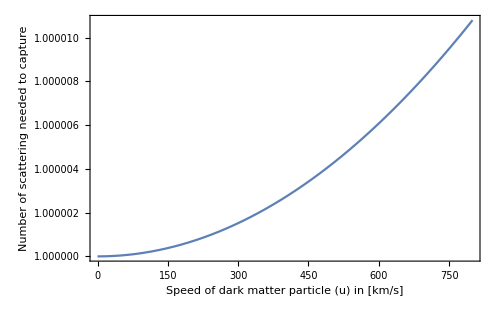

```mathematica
Plot[{nself[u]},{u,0,800},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

```mathematica
χ[p_,q_]:=Integrate[Exp[-y^2],{y,p,q}];
```

```mathematica
Series[(α^2-0.5)*χ[-α,α]+α*Exp[-α^2],{α,0,25}]
```

1.11022×10^-16 α+1.33333 α^3-0.266667 α^5+0.0571429 α^7-0.010582 α^9+0.0016835 α^11-0.0002331 α^13+0.00002849 α^15-3.11236×10^-6 α^17+3.0714×10^-7 α^19-2.76264×10^-8 α^21+2.28218×10^-9 α^23-1.74276×10^-10 α^25+O[α]^26

```mathematica
(*TIME EVOLUTION OF CAPTURED DARK MATTER DENSITY FOR VARIOUS DARK MATTER MASS*)
```

```mathematica
(*FOR EARTH *)
```

```mathematica
vesc=11.2*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
mn=50;(*in GeV*)(*average mass of nuclei is taken to be 50 GeV*)

μ[mx_]:=mx/mn;
```

```mathematica
nx[mx_]:=(3*10^5)/mx;(*in m^-3*)
```

```mathematica
μminus[mx_]:=(μ[mx]-1)/2;
Asq[mx_]:=3/2*vesc^2/vbar^2*μ[mx]/μminus[mx]^2;
```

```mathematica
n=10^29;(*in m^-3*)(*average density of earth is taken to be 5000 kg/m^3*)
```

```mathematica
σdmnu=10^-48;(*in m^2*) (*From XENON1T,LUX: dark matter nuclei interaction cross section can be found which is roughly 10^-48 m^2*)
```

```mathematica
σdmdm[mx_]:=10^-28*mx;(*in m^2*)(*From Bullet cluster dark matter dark matter self interaction cross section can be found which is roughly σ/mx=1 cm^2/g*)
```

```mathematica
a[mx_]:=(nx[mx]*(6/π)^0.5*σdmnu*n*vbar*vesc^2/vbar^2*(1-(1-Exp[-Asq[mx]])/Asq[mx]));
```

```mathematica
b[mx_]:=(nx[mx]*(6/π)^0.5*σdmdm[mx]*vbar*vesc^2/vbar^2*(1));
```

```mathematica
c[mx_]:=(nx[mx]*(6/π)^0.5*σdmdm[mx]*vbar*vesc^2/vbar^2*(-2/3*vbar^2/vesc^2));
```

```mathematica
mx1=10^-6;mx2=10^-4;mx3=10^-2;mx4=10^0;mx5=10^2;mx6=10^4;mx7=10^6;(*in GeV*)
```

```mathematica
sol2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2]+(b[mx2]+c[mx2])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→212.877-212.877 ⅇ^(-8.27452×10^-18 t)}}

```mathematica
capture2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.76146×10^-15 t}}

```mathematica
selfcap2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2]+b[mx2]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-101610.+101610. ⅇ^(1.73355×10^-20 t)}}

```mathematica
sol3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3]+(b[mx3]+c[mx3])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→175.27-175.27 ⅇ^(-8.27452×10^-18 t)}}

```mathematica
capture3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.45028×10^-15 t}}

```mathematica
selfcap3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3]+b[mx3]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-83659.3+83659.3 ⅇ^(1.73355×10^-20 t)}}

```mathematica
sol4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4]+(b[mx4]+c[mx4])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→182.415-182.415 ⅇ^(-8.27452×10^-18 t)}}

```mathematica
capture4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.5094×10^-15 t}}

```mathematica
selfcap4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4]+b[mx4]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-87069.8+87069.8 ⅇ^(1.73355×10^-20 t)}}

```mathematica
sol5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5]+(b[mx5]+c[mx5])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→174.229-174.229 ⅇ^(-8.27452×10^-18 t)}}

```mathematica
capture5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.44166×10^-15 t}}

```mathematica
selfcap5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5]+b[mx5]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-83162.4+83162.4 ⅇ^(1.73355×10^-20 t)}}

```mathematica
sol6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6]+(b[mx6]+c[mx6])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→0.00442411-0.00442411 ⅇ^(-8.27452×10^-18 t)}}

```mathematica
capture6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→3.66074×10^-20 t}}

```mathematica
selfcap6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6]+b[mx6]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-2.1117+2.1117 ⅇ^(1.73355×10^-20 t)}}

```mathematica
Plot[{nxtilde[t]/.sol2,nxtilde[t]/.selfcap2,nxtilde[t]/.capture2},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^-4 GeV",14],ImageSize->400,PlotLegends->{"Capture Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap2)/(nxtilde[t]/.capture2),(nxtilde[t]/.sol2)/(nxtilde[t]/.capture2)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^-4 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol3,nxtilde[t]/.selfcap3,nxtilde[t]/.capture3},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^-2 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap3)/(nxtilde[t]/.capture3),(nxtilde[t]/.sol3)/(nxtilde[t]/.capture3)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^-2 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol4,nxtilde[t]/.selfcap4,nxtilde[t]/.capture4},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^0 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap4)/(nxtilde[t]/.capture4),(nxtilde[t]/.sol4)/(nxtilde[t]/.capture4)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^0 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol5,nxtilde[t]/.selfcap5,nxtilde[t]/.capture5},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^2 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap5)/(nxtilde[t]/.capture5),(nxtilde[t]/.sol5)/(nxtilde[t]/.capture5)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^2 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol6,nxtilde[t]/.selfcap6,nxtilde[t]/.capture6},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^4 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap6)/(nxtilde[t]/.capture6),(nxtilde[t]/.sol6)/(nxtilde[t]/.capture6)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^4 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
(*TIME EVOLUTION OF CAPTURED DARK MATTER DENSITY FOR VARIOUS DARK MATTER MASS*)
```

```mathematica
(*FOR SUN *)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
mn=0.9;(*in GeV*)(*average mass of nuclei is taken to be 0.9 GeV*)

μ[mx_]:=mx/mn;
```

```mathematica
nx[mx_]:=(3*10^5)/mx;(*in m^-3*)
```

```mathematica
μminus[mx_]:=(μ[mx]-1)/2;
Asq[mx_]:=3/2*vesc^2/vbar^2*μ[mx]/μminus[mx]^2;
```

```mathematica
n=10^30;(*in m^-3*)(*average density of Sun is taken to be 1400 kg/m^3*)
```

```mathematica
σdmnu=10^-48;(*in m^2*) (*From XENON1T,LUX: dark matter nuclei interaction cross section can be found which is roughly 10^-48 m^2*)
```

```mathematica
σdmdm[mx_]:=10^-28*mx;(*in m^2*)(*From Bullet cluster dark matter dark matter self interaction cross section can be found which is roughly σ/mx=1 cm^2/g*)
```

```mathematica
a[mx_]:=(nx[mx]*(6/π)^0.5*σdmnu*n*vbar*vesc^2/vbar^2*(1-(1-Exp[-Asq[mx]])/Asq[mx]));
```

```mathematica
b[mx_]:=(nx[mx]*(6/π)^0.5*σdmdm[mx]*vbar*vesc^2/vbar^2*(1));
```

```mathematica
c[mx_]:=(nx[mx]*(6/π)^0.5*σdmdm[mx]*vbar*vesc^2/vbar^2*(-2/3*vbar^2/vesc^2));
```

```mathematica
mx1=10^-6;mx2=10^-4;mx3=10^-2;mx4=10^0;mx5=10^2;mx6=10^4;mx7=10^6;(*in GeV*)
```

```mathematica
sol2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2]+(b[mx2]+c[mx2])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.67696×10^11+1.67696×10^11 ⅇ^(4.44891×10^-17 t)}}

```mathematica
capture2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→7.46067×10^-6 t}}

```mathematica
selfcap2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2]+b[mx2]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.41351×10^11+1.41351×10^11 ⅇ^(5.2781×10^-17 t)}}

```mathematica
sol3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3]+(b[mx3]+c[mx3])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.56192×10^11+1.56192×10^11 ⅇ^(4.44891×10^-17 t)}}

```mathematica
capture3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→6.94883×10^-6 t}}

```mathematica
selfcap3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3]+b[mx3]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.31654×10^11+1.31654×10^11 ⅇ^(5.2781×10^-17 t)}}

```mathematica
sol4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4]+(b[mx4]+c[mx4])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.18586×10^10+1.18586×10^10 ⅇ^(4.44891×10^-17 t)}}

```mathematica
capture4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→5.2758×10^-7 t}}

```mathematica
selfcap4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4]+b[mx4]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.99564×10^9+9.99564×10^9 ⅇ^(5.2781×10^-17 t)}}

```mathematica
sol5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5]+(b[mx5]+c[mx5])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.28247×10^7+1.28247×10^7 ⅇ^(4.44891×10^-17 t)}}

```mathematica
capture5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→5.70558×10^-10 t}}

```mathematica
selfcap5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5]+b[mx5]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.08099×10^7+1.08099×10^7 ⅇ^(5.2781×10^-17 t)}}

```mathematica
sol6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6]+(b[mx6]+c[mx6])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1358.53+1358.53 ⅇ^(4.44891×10^-17 t)}}

```mathematica
capture6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→6.04397×10^-14 t}}

```mathematica
selfcap6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6]+b[mx6]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1145.1+1145.1 ⅇ^(5.2781×10^-17 t)}}

```mathematica
Plot[{nxtilde[t]/.sol2,nxtilde[t]/.selfcap2,nxtilde[t]/.capture2},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^-4 GeV",14],ImageSize->400,PlotLegends->{"Capture Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap2)/(nxtilde[t]/.capture2),(nxtilde[t]/.sol2)/(nxtilde[t]/.capture2)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Magenta,Orange},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^-4 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol3,nxtilde[t]/.selfcap3,nxtilde[t]/.capture3},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^-2 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap3)/(nxtilde[t]/.capture3),(nxtilde[t]/.sol3)/(nxtilde[t]/.capture3)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Magenta,Orange},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^-2 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol4,nxtilde[t]/.selfcap4,nxtilde[t]/.capture4},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^0 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap4)/(nxtilde[t]/.capture4),(nxtilde[t]/.sol4)/(nxtilde[t]/.capture4)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Magenta,Orange},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^0 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol5,nxtilde[t]/.selfcap5,nxtilde[t]/.capture5},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^2 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap5)/(nxtilde[t]/.capture5),(nxtilde[t]/.sol5)/(nxtilde[t]/.capture5)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Magenta,Orange},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^2 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[{nxtilde[t]/.sol6,nxtilde[t]/.selfcap6,nxtilde[t]/.capture6},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Green},PlotLabel-> Style["mx=10^4 GeV",14],ImageSize->400,PlotLegends->{"Capture,Self Capture and Evaporation","Capture and Self Capture","Capture"},FrameLabel->{Style["Time [sec]",FontSize->15],Style["Captured dark matter density",FontSize->15]}]
```

-Graphics-

```mathematica
Plot[{(nxtilde[t]/.selfcap4)/(nxtilde[t]/.capture4),(nxtilde[t]/.sol4)/(nxtilde[t]/.capture4)},{t,0,10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Magenta,Orange},PlotLegends->{"Self evaporation not included","Self evaporation included"},PlotLabel-> Style["mx=10^4 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
(*TIME EVOLUTION OF CAPTURED DARK MATTER DENSITY FOR VARIOUS DARK MATTER MASS*)
```

```mathematica
(*FOR NEUTRON STAR *)
```

```mathematica
vesc=10^5*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
mn=0.9;(*in GeV*)(*average mass of nuclei is taken to be 0.9 GeV*)

μ[mx_]:=mx/mn;
```

```mathematica
nx[mx_]:=(3*10^5)/mx;(*in m^-3*)
```

```mathematica
μminus[mx_]:=(μ[mx]-1)/2;
Asq[mx_]:=3/2*vesc^2/vbar^2*μ[mx]/μminus[mx]^2;
```

```mathematica
n=10^44;(*in m^-3*)(*average density of Neutron Star is taken to be 10^17 kg/m^3*)
```

```mathematica
σdmnu=10^-48;(*in m^2*) (*From XENON1T,LUX: dark matter nuclei interaction cross section can be found which is roughly 10^-48 m^2*)
```

```mathematica
σdmdm[mx_]:=10^-28*mx;(*in m^2*)(*From Bullet cluster dark matter dark matter self interaction cross section can be found which is roughly σ/mx=1 cm^2/g*)
```

```mathematica
a[mx_]:=(nx[mx]*(6/π)^0.5*σdmnu*n*vbar*vesc^2/vbar^2*(1-(1-Exp[-Asq[mx]])/Asq[mx]));
```

```mathematica
b[mx_]:=(nx[mx]*(6/π)^0.5*σdmdm[mx]*vbar*vesc^2/vbar^2*(1));
```

```mathematica
c[mx_]:=(nx[mx]*(6/π)^0.5*σdmdm[mx]*vbar*vesc^2/vbar^2*(-2/3*vbar^2/vesc^2));
```

```mathematica
mx1=10^-6;mx2=10^-4;mx3=10^-2;mx4=10^0;mx5=10^2;mx6=10^4;mx7=10^6;(*in GeV*)
```

```mathematica
sol2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2]+(b[mx2]+c[mx2])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.86509×10^27+9.86509×10^27 ⅇ^(1.38197×10^-12 t)}}

```mathematica
capture2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.36332×10^16 t}}

```mathematica
selfcap2=FullSimplify[DSolve[{nxtilde'[t]==a[mx2]+b[mx2]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.86503×10^27+9.86503×10^27 ⅇ^(1.38198×10^-12 t)}}

```mathematica
sol3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3]+(b[mx3]+c[mx3])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.99874×10^25+9.99874×10^25 ⅇ^(1.38197×10^-12 t)}}

```mathematica
capture3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.38179×10^14 t}}

```mathematica
selfcap3=FullSimplify[DSolve[{nxtilde'[t]==a[mx3]+b[mx3]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.99868×10^25+9.99868×10^25 ⅇ^(1.38198×10^-12 t)}}

```mathematica
sol4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4]+(b[mx4]+c[mx4])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.00001×10^24+1.00001×10^24 ⅇ^(1.38197×10^-12 t)}}

```mathematica
capture4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.38198×10^12 t}}

```mathematica
selfcap4=FullSimplify[DSolve[{nxtilde'[t]==a[mx4]+b[mx4]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-1.×10^24+1.×10^24 ⅇ^(1.38198×10^-12 t)}}

```mathematica
sol5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5]+(b[mx5]+c[mx5])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.99842×10^21+9.99842×10^21 ⅇ^(1.38197×10^-12 t)}}

```mathematica
capture5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.38175×10^10 t}}

```mathematica
selfcap5=FullSimplify[DSolve[{nxtilde'[t]==a[mx5]+b[mx5]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.99836×10^21+9.99836×10^21 ⅇ^(1.38198×10^-12 t)}}

```mathematica
sol6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6]+(b[mx6]+c[mx6])*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.83342×10^19+9.83342×10^19 ⅇ^(1.38197×10^-12 t)}}

```mathematica
capture6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→1.35895×10^8 t}}

```mathematica
selfcap6=FullSimplify[DSolve[{nxtilde'[t]==a[mx6]+b[mx6]*nxtilde[t],nxtilde[0]==0},nxtilde[t],t]]
```

{{nxtilde[t]→-9.83336×10^19+9.83336×10^19 ⅇ^(1.38198×10^-12 t)}}

```mathematica
Plot[(nxtilde[t]/.selfcap2)/(nxtilde[t]/.sol2),{t,0,4*10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotLabel-> Style["mx=10^-4 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style[" Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[(nxtilde[t]/.selfcap3)/(nxtilde[t]/.sol3),{t,0,4*10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotLabel-> Style["mx=10^-2 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style[" Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[(nxtilde[t]/.selfcap4)/(nxtilde[t]/.sol4),{t,0,4*10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotLabel-> Style["mx=10^0 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style[" Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[(nxtilde[t]/.selfcap5)/(nxtilde[t]/.sol5),{t,0,4*10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotLabel-> Style["mx=10^2 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style[" Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
Plot[(nxtilde[t]/.selfcap6)/(nxtilde[t]/.sol6),{t,0,4*10^17},Frame->True,PlotRangePadding->None,FrameStyle->Directive[14, "Times",Black],PlotLabel-> Style["mx=10^-4 GeV",14],FrameLabel->{Style["Time [sec]",FontSize->15],Style[" Ratio of captured dark matter density",FontSize->15]},ImageSize->500]
```

-Graphics-

```mathematica
(*ANALYSIS IN Subscript[σ, XX] - Subscript[m, X] PLANE *)
```

```mathematica
(*FOR SUN *)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
b=(ρx/mx*(6/π)^0.5*σdmdm*vbar*vesc^2/vbar^2*(1-2/3*vbar^2/vesc^2));
```

```mathematica
bprime=(ρx/mx*(6/π)^0.5*σdmdm*vbar*vesc^2/vbar^2*(1));
```

```mathematica
t0=1.5*10^17;(*Age of the Sun in sec*)

β01=1.1;β02=3;β03=10;β04=100;(*Enhancement factors when self evaporation is included*)
```

```mathematica
βprime01=1.1;βprime02=3;βprime03=10;βprime04=100;(*Enhancement factors when self evaporation is not included*)
```

```mathematica
βratio1=0.2;βratio2=0.3;βratio3=0.5;βratio4=0.7;(*βratio=β/βprime*)
```

```mathematica
(b*t0)
```

(6.67337×10^28 σdmdm)/mx

```mathematica
(bprime*t0)
```

(7.91715×10^28 σdmdm)/mx

```mathematica
a=6.67337*10^28;
aprime=7.91715*10^28;
```

```mathematica
conv=1.78*10^-28;(*conversion factor*)
```

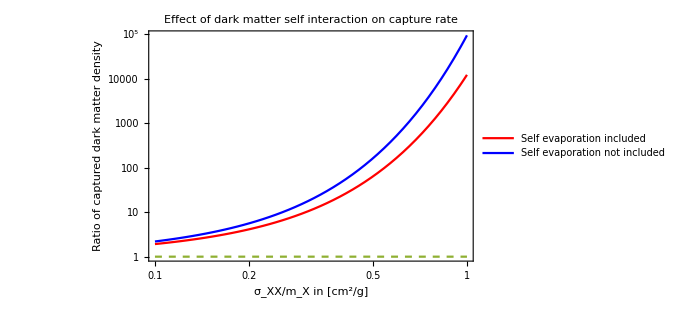

```mathematica
LogLogPlot[{(Exp[a*conv*x]-1)/(a*x*conv),(Exp[aprime*conv*x]-1)/(aprime*x*conv),1},{x,0.1,1.0},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotLabel-> Style["Effect of dark matter self interaction on capture rate",14],FrameLabel->{Style["σ_XX/m_X in [cm^2/g] ",FontSize->20],Style["Ratio of captured dark matter density",FontSize->15]},PlotStyle->{Red,Blue,Dashed},PlotLegends->Placed[{"Self evaporation  included","Self evaporation not included"},{0.30,0.70}],ImageSize->500]
```

```mathematica
myticks={{{{-25,"10^-25"},{-26,"10^-26"},{-27,"10^-27"},{-28,"10^-28"}},None},{{{2,"100"},{3,"1000"}},None}};
```

```mathematica
plot1=ContourPlot[{a*10^y/10^x==Log[1+β01*a*10^y/10^x],a*10^y/10^x==Log[1+β02*a*10^y/10^x],a*10^y/10^x==Log[1+β03*a*10^y/10^x],a*10^y/10^x==Log[1+β04*a*10^y/10^x]},{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,ContourStyle->{Blue,Red,Magenta,Orange},PlotLegends->{"Enhancement factor=1.1","Enhancement factor=3","Enhancement factor=10","Enhancement factor=100"},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]},PlotLabel-> Style["Self evaporation included",14]];
```

```mathematica
plot2=RegionPlot[10^y-1.78*10^-28*10^x>0,{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,PlotStyle->Brown,BoundaryStyle->Brown,FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]},FrameStyle->Directive[14, "Times",Black]];
```

```mathematica
plot3=ContourPlot[{aprime*10^y/10^x==Log[1+βprime01*aprime*10^y/10^x],aprime*10^y/10^x==Log[1+βprime02*aprime*10^y/10^x],aprime*10^y/10^x==Log[1+βprime03*aprime*10^y/10^x],aprime*10^y/10^x==Log[1+βprime04*aprime*10^y/10^x]},{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,ContourStyle->{Blue,Red,Magenta,Orange},PlotLegends->{"Enhancement factor=1.1","Enhancement factor=3","Enhancement factor=10","Enhancement factor=100"},PlotLabel-> Style["Self evaporation not included",14],FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]}];
```

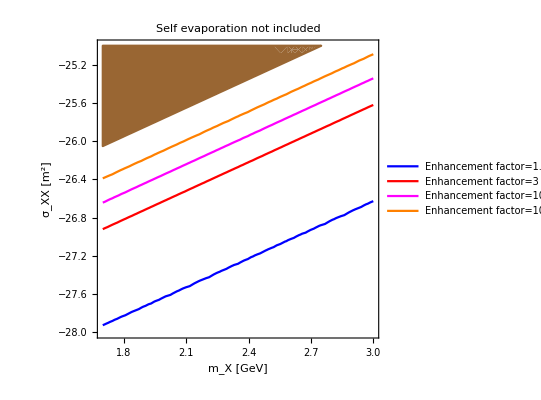

```mathematica
Show[plot3,plot2]
```

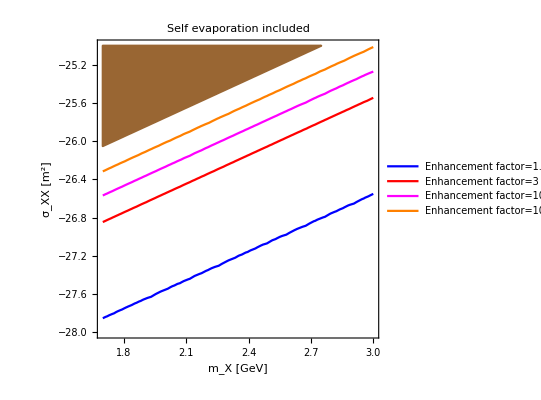

```mathematica
Show[plot1,plot2]
```

```mathematica
plot4=ContourPlot[{βratio1==aprime/a*(Exp[a*10^y/10^x]-1)/(Exp[aprime*10^y/10^x]-1),βratio2==aprime/a*(Exp[a*10^y/10^x]-1)/(Exp[aprime*10^y/10^x]-1),βratio3==aprime/a*(Exp[a*10^y/10^x]-1)/(Exp[aprime*10^y/10^x]-1),βratio4==aprime/a*(Exp[a*10^y/10^x]-1)/(Exp[aprime*10^y/10^x]-1)},{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,ContourStyle->{Blue,Red,Magenta,Orange},FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]},PlotLegends->{"Change in Enhancement factor by 80%","Change in Enhancement factor by 70%","Change in Enhancement factor by 50%","Change in Enhancement factor by 30%"},FrameStyle->Directive[14, "Times",Black]];
```

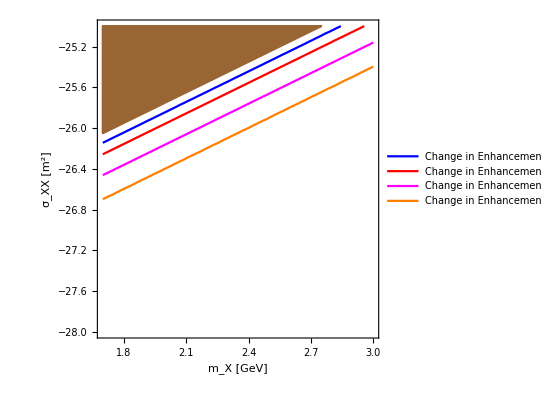

```mathematica
Show[plot4,plot2]
```

```mathematica
(*ANALYSIS IN Subscript[σ, XX] - Subscript[m, X] PLANE *)
```

```mathematica
(*FOR EARTH*)
```

```mathematica
vesc=11.2*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
b=(ρx/mx*(6/π)^0.5*σdmdm*vbar*vesc^2/vbar^2*(1-2/3*vbar^2/vesc^2));
```

```mathematica
bprime=(ρx/mx*(6/π)^0.5*σdmdm*vbar*vesc^2/vbar^2*(1));
```

```mathematica
t0=1.5*10^17;(*Age of the Sun in sec*)
β01=0.5;β02=0.7;β03=0.8;β04=0.9;
βprime01=1.1;βprime02=3;βprime03=5;βprime04=10;
```

```mathematica
(b*t0)
```

-(1.24118×10^28 σdmdm)/mx

```mathematica
(bprime*t0)
```

(2.60033×10^25 σdmdm)/mx

```mathematica
a=-1.24118*10^28;(*in Gev/m^2*)
aprime=2.6033*10^28;(*in Gev/m^2*)
```

```mathematica
conv=1.78*10^-28;(*conversion factor*)
```

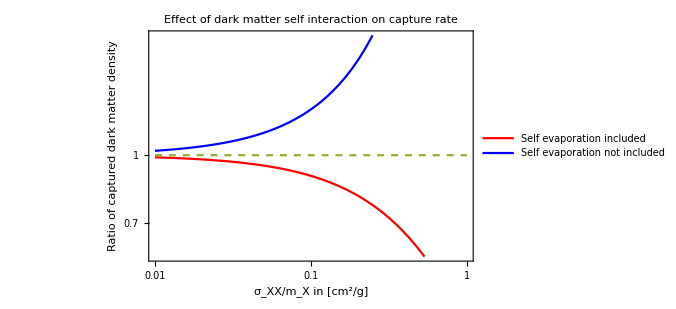

```mathematica
LogLogPlot[{(Exp[a*conv*x]-1)/(a*x*conv),(Exp[aprime*conv*x]-1)/(aprime*x*conv),1},{x,0.01,1},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["σ_XX/m_X in [cm^2/g] ",FontSize->20],Style["Ratio of captured dark matter density",FontSize->15]},PlotLabel-> Style["Effect of dark matter self interaction on capture rate",14],PlotStyle->{Red,Blue,Dashed},PlotLegends->Placed[{"Self evaporation  included","Self evaporation not included"},{0.25,0.20}],ImageSize->500]
```

```mathematica
myticks={{{{-25,"10^-25"},{-26,"10^-26"},{-27,"10^-27"},{-28,"10^-28"}},None},{{{2,"100"},{3,"1000"}},None}};
```

```mathematica
plot1=ContourPlot[{a*10^y/10^x==Log[1+β01*a*10^y/10^x],a*10^y/10^x==Log[1+β02*a*10^y/10^x],a*10^y/10^x==Log[1+β03*a*10^y/10^x],a*10^y/10^x==Log[1+β04*a*10^y/10^x]},{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,ContourStyle->{Blue,Red,Magenta,Orange},PlotLabel-> Style["Self evaporation included",14],FrameTicks->myticks,PlotLegends->{"Reduction factor=0.5","Reduction factor=0.7","Reduction factor=0.8","Reduction factor=0.9"},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]}];
```

```mathematica
plot2=RegionPlot[10^y-1.78*10^-28*10^x>0,{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,FrameTicks->myticks,PlotStyle->Brown,BoundaryStyle->Brown,FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]},FrameStyle->Directive[14, "Times",Black]];
```

```mathematica
plot3=ContourPlot[{aprime*10^y/10^x==Log[1+βprime01*aprime*10^y/10^x],aprime*10^y/10^x==Log[1+βprime02*aprime*10^y/10^x],aprime*10^y/10^x==Log[1+βprime03*aprime*10^y/10^x],aprime*10^y/10^x==Log[1+βprime04*aprime*10^y/10^x]},{x,Log10[50],Log10[1000]},{y,Log10[10^-25],Log10[10^-28]},Frame->True,PlotRangePadding->None,ContourStyle->{Blue,Red,Magenta,Orange},PlotLabel-> Style["Self evaporation not included",14],FrameTicks->myticks,PlotLegends->{"Enhancement factor=1.1","Enhancement factor=3","Enhancement factor=5","Enhancement factor=10"},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_X [GeV]",FontSize->20],Style["σ_XX [m^2]",FontSize->20]}];
```

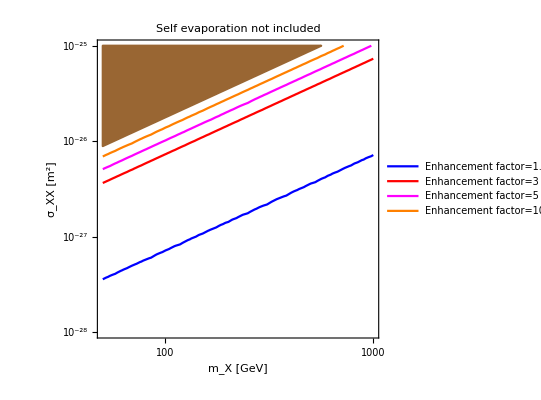

```mathematica
Show[plot3,plot2]
```

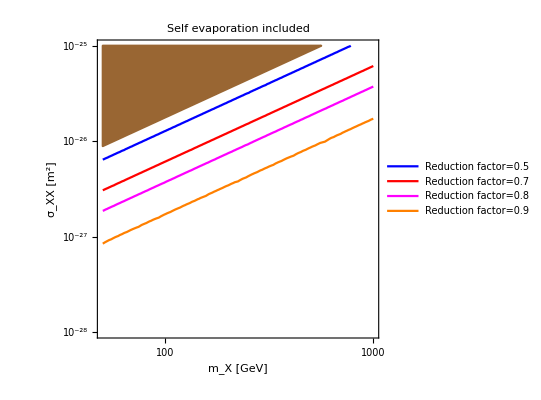

```mathematica
Show[plot1,plot2]
```

```mathematica
(*VARIATION WITH ESCAPE VELOCITY*)
```

```mathematica
vbar=300*10^3;(*in m/sec*)
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
ratio=1.78*10^-28;(*in m^2*)(*From Bullet cluster dark matter dark matter self interaction cross section can be found which is roughly σ/mx=1 cm^2/g*)
```

```mathematica
b[vesc_]:=(ρx*(6/π)^0.5*ratio*vbar*vesc^2/vbar^2*(1-2/3*vbar^2/vesc^2));
```

```mathematica
bprime[vesc_]:=(ρx*(6/π)^0.5*ratio*vbar*vesc^2/vbar^2);
```

```mathematica
t0=1.5*10^17;
```

```mathematica
β[vesc_]:=(Exp[b[vesc]*t0]-1)/(b[vesc]*t0);
```

```mathematica
βprime[vesc_]:=(Exp[bprime[vesc]*t0]-1)/(bprime[vesc]*t0);
```

```mathematica
myticks={{Automatic,None},{{{1000,"1"},{10^4,"10"},{10^5,"100"},{10^6,"1000"},{10^7,"10^4"},{10^8,"10^5"}},None}};
```

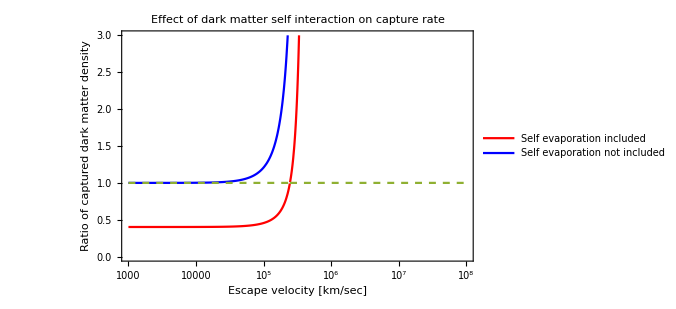

```mathematica
LogLinearPlot[{β[vesc],βprime[vesc],1},{vesc,10^3,10^8},PlotRange->{0,3},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotStyle->{Red,Blue,Dashed},PlotLabel-> Style["Effect of dark matter self interaction on capture rate",14],FrameTicks->myticks,FrameLabel->{Style["Escape velocity [km/sec]",FontSize->15],Style["Ratio of captured dark matter density",FontSize->15]},PlotLegends->Placed[{"Self evaporation  included","Self evaporation not included"},{0.75,0.65}],ImageSize->500]
```

```mathematica
(*MULTIPLE CAPTURE FOR SUN*)
```

```mathematica
vesc=618 (* in km/s*);
```

```mathematica
kb=1.38*10^-23;(*in J/K*)
T=1.57*10^7;(*in K*)
```

```mathematica
mn=1;(*in Gev*)
```

```mathematica
mx1=10^4;mx2=10^5;mx3=10^6;mx4=10^7;mx5=10^8;(*in Gev*)
```

```mathematica
βplus[mx_]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
ϵ=10^-4;
```

```mathematica
mevap=(3*kb*T)/((vesc*10^3)^2)*5.62*10^26(*in Gev*)
```

0.956444

```mathematica
n[u_,mx_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/(1-βplus[mx])]/βplus[mx]];

nbra[u_,mx_]:=Log[vesc^2/(u^2+vesc^2)]/Log[1-βplus[mx]/2];
nself[u_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/ϵ]];
```

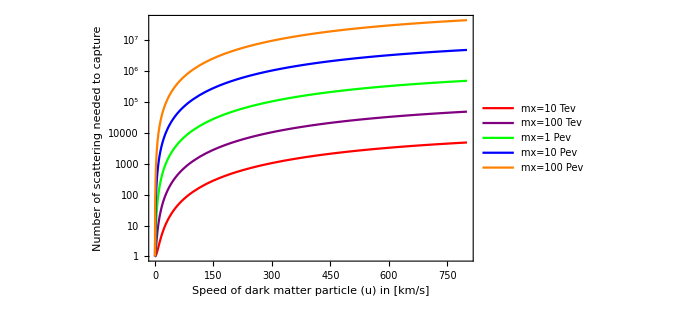

```mathematica
plot1=LogPlot[{n[u,mx1],n[u,mx2],n[u,mx3],n[u,mx4],n[u,mx5]},{u,0,800},PlotRange->All,PlotStyle->{Red,Purple,Green,Blue,Orange},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}]
```

```mathematica
plot2=LogPlot[{nbra[u,mx1],nbra[u,mx2],nbra[u,mx3],nbra[u,mx4],nbra[u,mx5]},{u,0,800},PlotRange->{1,10^8},PlotStyle->{Directive[Red,Dashed],Directive[Purple,Dashed],Directive[Green,Dashed],Directive[Blue,Dashed],Directive[Orange,Dashed]},Frame->True,FrameLabel->{Style["Speed of dark matter particle at infinity in [km/s] ",FontSize->20],Style["Maximum  number of scattering",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}];
```

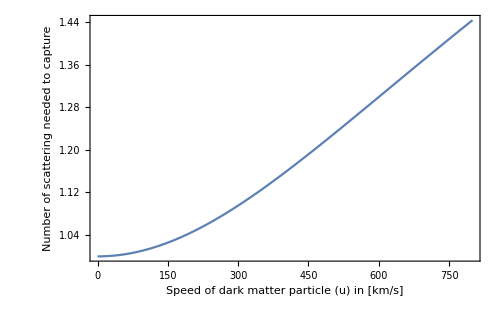

```mathematica
Plot[{nself[u]},{u,0,800},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

```mathematica
(*MULTIPLE CAPTURE FOR EARTH*)
```

```mathematica
vesc=11.2 (* in km/s*);
```

```mathematica
mn=50;(*in Gev*)
```

```mathematica
kb=1.38*10^-23;(*in J/K*)
T=6000;(*in K*)
```

```mathematica
mx1=10^4;mx2=10^5;mx3=10^6;mx4=10^7;mx5=10^8;(*in Gev*)
```

```mathematica
βplus[mx_]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
ϵ=10^-4;
```

```mathematica
mevap=(3*kb*T)/((vesc*10^3)^2)*5.62*10^26(*in Gev*)
```

1.11289

```mathematica
n[u_,mx_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/(1-βplus[mx])]/βplus[mx]];
nbra[u_,mx_]:=Log[vesc^2/(u^2+vesc^2)]/Log[1-βplus[mx]/2];
nself[u_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/ϵ]];
```

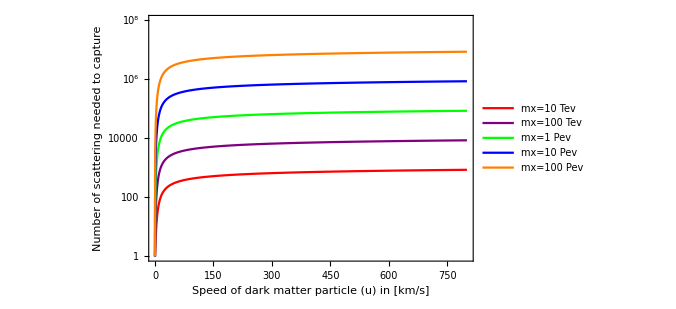

```mathematica
plot1=LogPlot[{n[u,mx1],n[u,mx2],n[u,mx3],n[u,mx4],n[u,mx5]},{u,0,800},PlotRange->{1,10^8},PlotStyle->{Red,Purple,Green,Blue,Orange},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}]
```

```mathematica
plot2=LogPlot[{nbra[u,mx1],nbra[u,mx2],nbra[u,mx3],nbra[u,mx4],nbra[u,mx5]},{u,0,800},PlotRange->{1,10^8},PlotStyle->{Directive[Red,Dashed],Directive[Purple,Dashed],Directive[Green,Dashed],Directive[Blue,Dashed],Directive[Orange,Dashed]},Frame->True,FrameLabel->{Style["Speed of dark matter particle at infinity in [km/s] ",FontSize->20],Style["Maximum  number of scattering",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"mx=10 Tev","mx=100 Tev","mx=1 Pev","mx=10 Pev","mx=100 Pev"}];
```

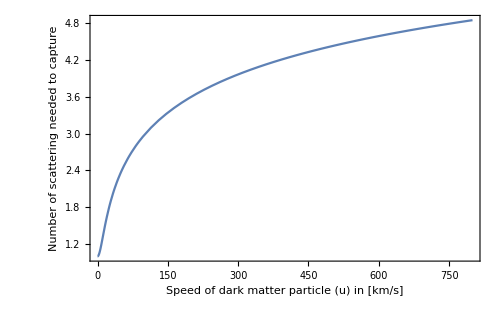

```mathematica
Plot[{nself[u]},{u,0,800},Frame->True,FrameLabel->{Style["Speed of dark matter particle (u) in [km/s] ",FontSize->20],Style["Number of scattering needed to capture",FontSize->20]},FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

```mathematica
(*VARIATION OF MULTI SELF CAPTURE WITH ESCAPE VELOCITY*)
```

```mathematica
u=1000;(*in km/s*)
```

```mathematica
ϵ=10^-6;
```

```mathematica
nself[vesc_]:=1+Log[(u^2+vesc^2)/vesc^2]/Log[Log[1/ϵ]];
```

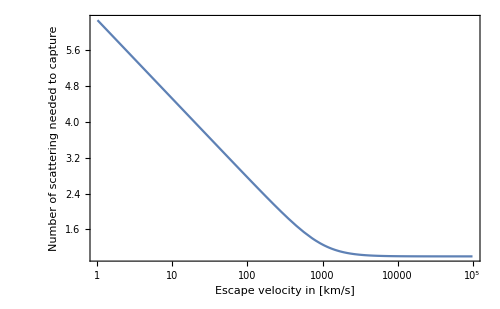

```mathematica
LogLinearPlot[{nself[vesc]},{vesc,1,10^5},Frame->True,PlotRange->All,FrameLabel->{Style["Escape velocity in [km/s] ",FontSize->12],Style["Number of scattering needed to capture",FontSize->12]},FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

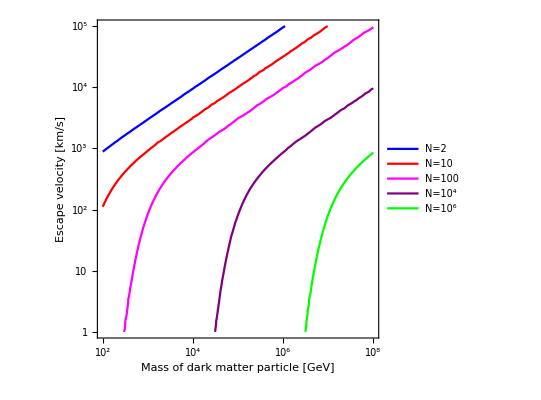

```mathematica
(*VARIATION OF  SELF CAPTURE WITH ESCAPE VELOCITY*)

u=600;(*in km/s*)
mn=20;(*in GeV*)
N1=2;N2=10;N3=100;N4=10^4;N5=10^6;
Nbra1=2;Nbra2=10;Nbra3=100;Nbra4=10^4;Nbra5=10^6;
myticks={{{{5,"10^5"},{4,"10^4"},{3,"10^3"},{2,"10^2"},{1,"10"},{0,"1"}},None},{{{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
plot1=ContourPlot[{N1==1+Log[(u^2+(10^vesc)^2)/((10^vesc)^2)]/Log[Log[1/(1-(4*10^mx*mn)/((10^mx+mn)^2))]/((4*10^mx*mn)/((10^mx+mn)^2))],N2==1+Log[(u^2+(10^vesc)^2)/((10^vesc)^2)]/Log[Log[1/(1-(4*10^mx*mn)/((10^mx+mn)^2))]/((4*10^mx*mn)/((10^mx+mn)^2))],N3==1+Log[(u^2+(10^vesc)^2)/((10^vesc)^2)]/Log[Log[1/(1-(4*10^mx*mn)/((10^mx+mn)^2))]/((4*10^mx*mn)/((10^mx+mn)^2))],N4==1+Log[(u^2+(10^vesc)^2)/((10^vesc)^2)]/Log[Log[1/(1-(4*10^mx*mn)/((10^mx+mn)^2))]/((4*10^mx*mn)/((10^mx+mn)^2))],N5==1+Log[(u^2+(10^vesc)^2)/((10^vesc)^2)]/Log[Log[1/(1-(4*10^mx*mn)/((10^mx+mn)^2))]/((4*10^mx*mn)/((10^mx+mn)^2))]},{mx,Log10[100],Log10[10^8]},{vesc,Log10[1],Log10[10^5]},Frame->True,PlotRangePadding->None,ContourStyle->{Blue,Red,Magenta,Purple,Green},FrameLabel->{Style["Mass of dark matter particle [GeV]",FontSize->20],Style["Escape velocity [km/s]",FontSize->20]},FrameTicks->myticks,FrameStyle->Directive[14, "Times",Black],PlotLegends->{"N=2","N=10","N=100","N=10^4","N=10^6"},ImageSize->400]
```

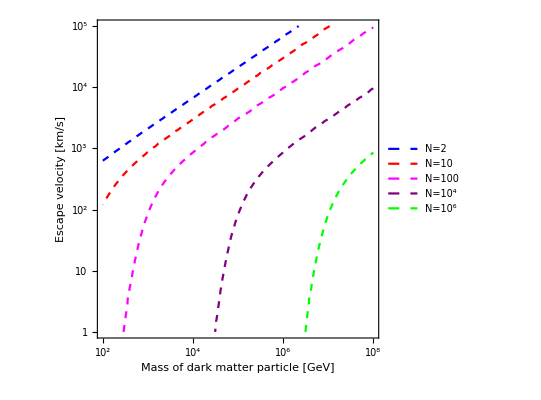

```mathematica
plot2=ContourPlot[{Nbra1==Log[((10^vesc)^2)/(u^2+(10^vesc)^2)]/Log[1-0.5*(4*10^mx*mn)/((10^mx+mn)^2)],Nbra2==Log[((10^vesc)^2)/(u^2+(10^vesc)^2)]/Log[1-0.5*(4*10^mx*mn)/((10^mx+mn)^2)],Nbra3==Log[((10^vesc)^2)/(u^2+(10^vesc)^2)]/Log[1-0.5*(4*10^mx*mn)/((10^mx+mn)^2)],Nbra4==Log[((10^vesc)^2)/(u^2+(10^vesc)^2)]/Log[1-0.5*(4*10^mx*mn)/((10^mx+mn)^2)],Nbra5==Log[((10^vesc)^2)/(u^2+(10^vesc)^2)]/Log[1-0.5*(4*10^mx*mn)/((10^mx+mn)^2)]},{mx,Log10[100],Log10[10^8]},{vesc,Log10[1],Log10[10^5]},Frame->True,PlotRangePadding->None,ContourStyle->{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Magenta,Dashed],Directive[Purple,Dashed],Directive[Green,Dashed]},FrameLabel->{Style["Mass of dark matter particle [GeV]",FontSize->20],Style["Escape velocity [km/s]",FontSize->20]},FrameTicks->myticks,FrameStyle->Directive[14, "Times",Black],PlotLegends->{"N=2","N=10","N=100","N=10^4","N=10^6"},ImageSize->400]
```

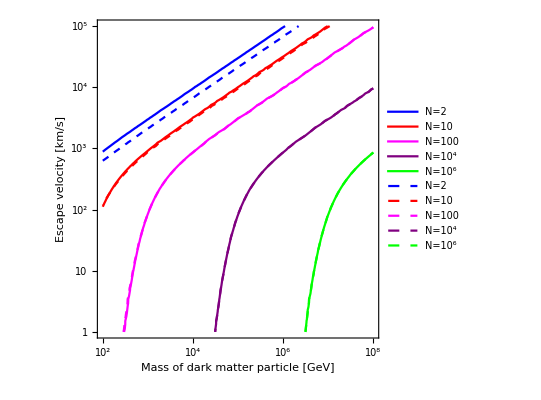

```mathematica
Show[plot1,plot2]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR SUN  WITH NUCLEI*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
vtilde=250*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
t=1.5 10^17(*Age  in sec*);
n=10^30;(*in m^-3*)(*average density of Sun is taken to be 1400 kg/m^3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn;
```

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/Factorial[N]*NIntegrate[y *Exp[-y *tau[sigma]]*(y* tau[sigma])^N,{y,0,1}];
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12]
```

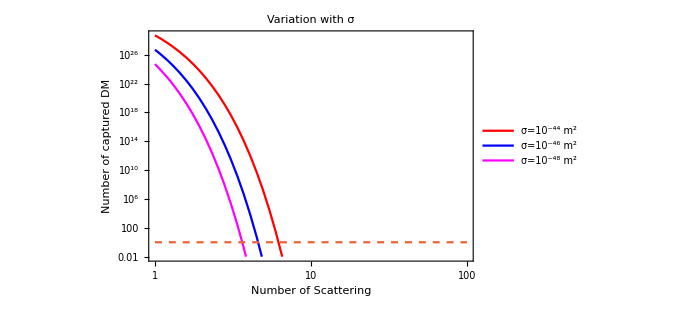

```mathematica
LogLogPlot[{t* CNNboosted[x,10^7,10^-44],t* CNNboosted[x,10^7,10^-46],t* CNNboosted[x,10^7,10^-48],1},{x,1,100},PlotStyle->{Red,Blue,Magenta,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,PlotLabel->"Variation with σ",FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],PlotLegends->{"σ=10^-44 m^2","σ=10^-46 m^2","σ=10^-48 m^2"},ImageSize->500]
```

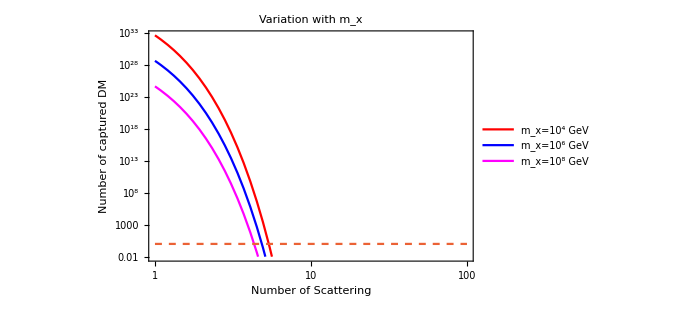

```mathematica
LogLogPlot[{t* CNNboosted[x,10^4,10^-46],t* CNNboosted[x,10^6,10^-46],t* CNNboosted[x,10^8,10^-46],1},{x,1,100},PlotStyle->{Red,Blue,Magenta,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},PlotLabel->"Variation with m_x",FrameStyle->Directive[14, "Times",Black],PlotLegends->{"m_x=10^4 GeV","m_x=10^6 GeV","m_x=10^8 GeV"},ImageSize->500]
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

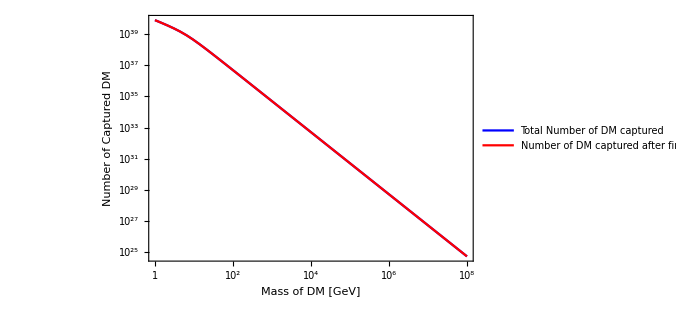

```mathematica
LogPlot[{Ctotalnew[10^x,10^-46],t*CNNboosted[1,10^x,10^-46]},{x,0,8},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

```mathematica
myticks2={{Automatic,None},{{{38,"10^-38"},{42,"10^-42"},{46,"10^-46"}},None}};
```

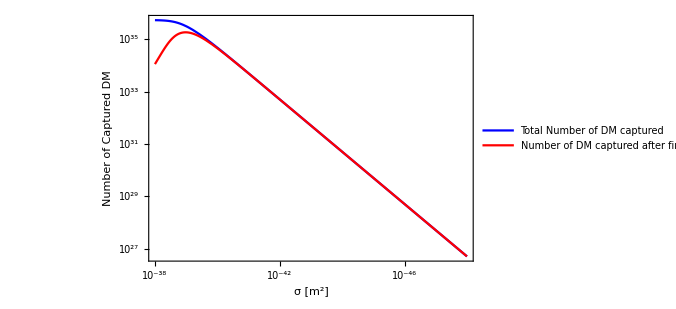

```mathematica
LogPlot[{Ctotalnew[10^6,10^-x],t*CNNboosted[1,10^6,10^-x]},{x,38,48},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks2,FrameLabel->{Style["σ [m^2]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{"Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR EARTH WITH NUCLEI*)
```

```mathematica
R=6400*10^3;(*in m*)
```

```mathematica
vesc=11.2*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
vtilde=250*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
mn=50;(*in GeV*)
```

```mathematica
t=1.5 10^17(*Age  in sec*);
n=10^30;(*in m^-3*)(*average density of Earth is taken to be 5000 kg/m^3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn;
```

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/Factorial[N]*NIntegrate[y *Exp[-y *tau[sigma]]*(y* tau[sigma])^N,{y,0,1}];
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12]
```

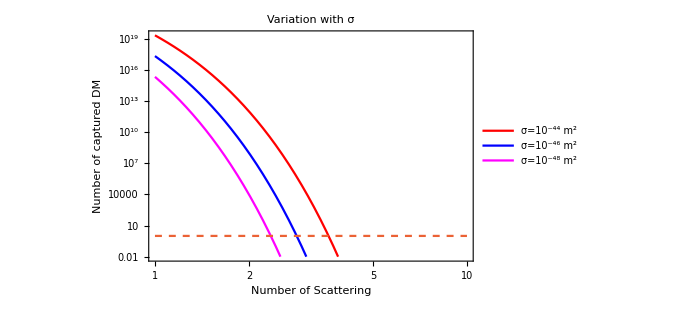

```mathematica
LogLogPlot[{t* CNNboosted[x,10^6,10^-44],t* CNNboosted[x,10^6,10^-46],t* CNNboosted[x,10^6,10^-48],1},{x,1,10},PlotStyle->{Red,Blue,Magenta,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,PlotLabel->"Variation with σ",FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],PlotLegends->{"σ=10^-44 m^2","σ=10^-46 m^2","σ=10^-48 m^2"},ImageSize->500];
```

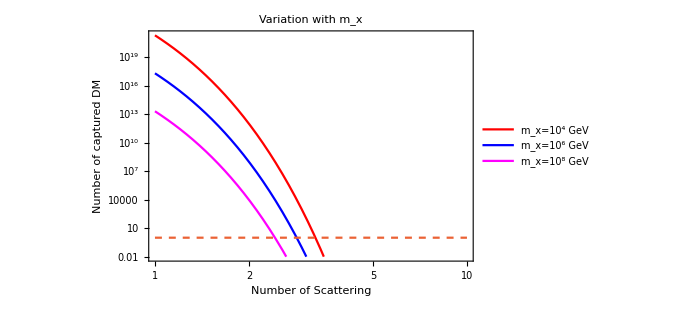

```mathematica
LogLogPlot[{t* CNNboosted[x,10^4,10^-46],t* CNNboosted[x,10^6,10^-46],t* CNNboosted[x,10^8,10^-46],1},{x,1,10},PlotStyle->{Red,Blue,Magenta,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},PlotLabel->"Variation with m_x",FrameStyle->Directive[14, "Times",Black],PlotLegends->{"m_x=10^4 GeV","m_x=10^6 GeV","m_x=10^8 GeV"},ImageSize->500];
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^2,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

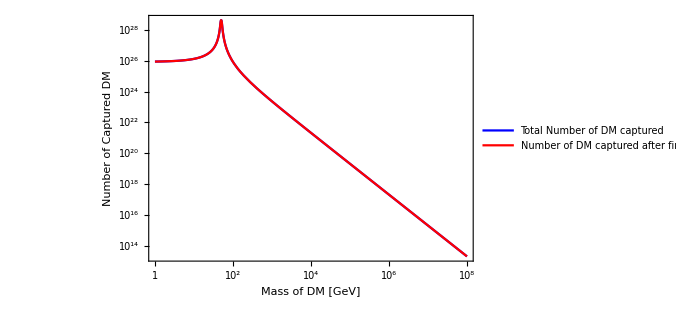

```mathematica
LogPlot[{Ctotalnew[10^x,10^-46],t*CNNboosted[1,10^x,10^-46]},{x,0,8},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR NEUTRON STAR WITH NUCLEI*)
```

```mathematica
R=10^4;(*in m*)
```

```mathematica
vesc=10^5*10^3;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
vtilde=247*10^3(*in m/sec*);
```

```mathematica
ρx=0.3*10^6;(*in GeV/m^3*)
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^44;(*in m^-3*)(*average density of Neutron Star is taken to be 10^17 kg/m^3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

7.5×10^-49

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->20];
```

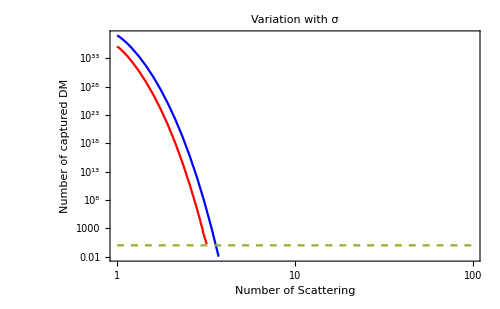

```mathematica
LogLogPlot[{t* CNNboosted[x,10^4,10^-49],t* CNNboosted[x,10^4,10^-51],1},{x,1,100},PlotStyle->{Blue,Red,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},PlotLabel->"Variation with σ",FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

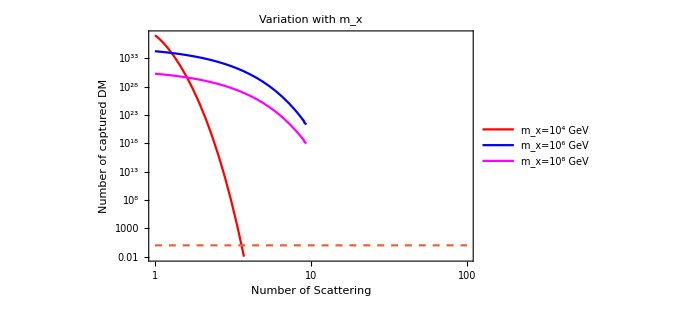

```mathematica
LogLogPlot[{t* CNNboosted[x,10^4,10^-49],t* CNNboosted[x,10^6,10^-49],t* CNNboosted[x,10^8,10^-49],1},{x,1,100},PlotStyle->{Red,Blue,Magenta,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},PlotLabel->"Variation with m_x",FrameStyle->Directive[14, "Times",Black],PlotLegends->{"m_x=10^4 GeV","m_x=10^6 GeV","m_x=10^8 GeV"},ImageSize->500]
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*Sum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

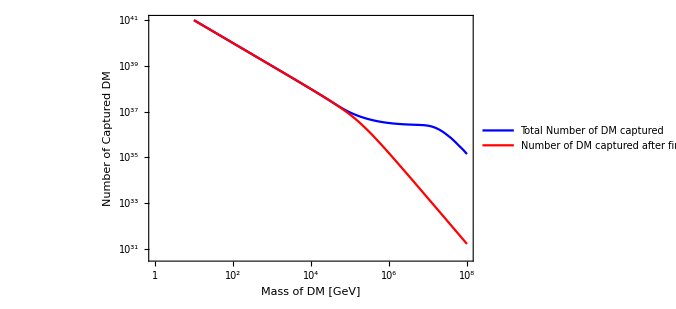

```mathematica
ListLogPlot[{Table[{x,Ctotalnew[10^x,10^-46]},{x,1,8,0.1}],Table[{x,t*CNNboosted[1,10^x,10^-46]},{x,1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

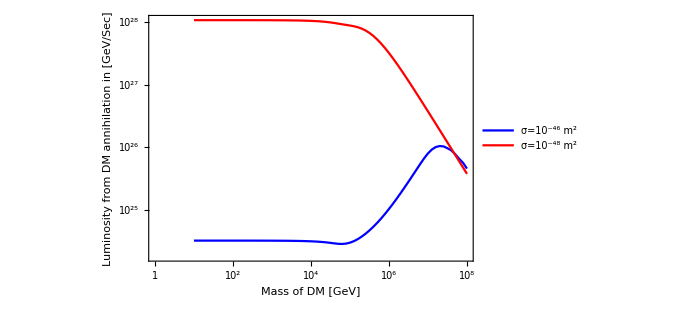

```mathematica
ListLogPlot[{Table[{x,10^x/t*Ctotalnew[10^x,10^-46]},{x,1,8,0.1}],Table[{x,10^x/t*Ctotalnew[10^x,10^-48]},{x,1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,PlotLegends->{"σ=10^-46 m^2","σ=10^-48 m^2"},FrameLabel->{Style["Mass of DM [GeV]",FontSize->15,Bold],Style["Luminosity from DM annihilation in [GeV/Sec]",FontSize->15,Bold]},ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR WHITE DWARF WITH NUCLEI*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
vtilde=247*10^3(*in m/sec*);
```

```mathematica
ρx=0.3*10^6;(*in GeV/m^3*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)(*average density of Neutron Star is taken to be 10^17 kg/m^3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

1.07143×10^-43

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]}];
```

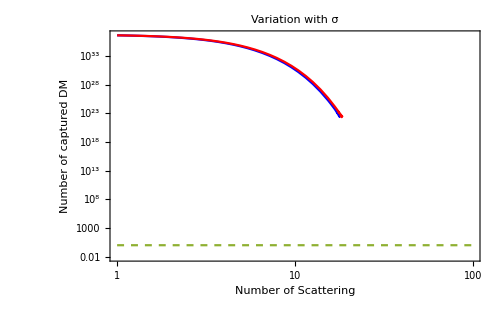

```mathematica
LogLogPlot[{t* CNNboosted[x,10^6,10^-43],t* CNNboosted[x,10^6,10^-42],1},{x,1,100},PlotStyle->{Blue,Red,Dashed},PlotRange->{Automatic,{0.01,Automatic}},Frame->True,FrameLabel->{Style["Number of Scattering",FontSize->20,Bold],Style["Number of captured DM",FontSize->20,Bold]},PlotLabel->"Variation with σ",FrameStyle->Directive[14, "Times",Black],ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR SUN  WITH ELECTRON*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
vtilde=250*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=1.5 10^17(*Age  in sec*);
n=10^34;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn;
```

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/Factorial[N]*NIntegrate[y *Exp[-y *tau[sigma]]*(y* tau[sigma])^N,{y,0,1}];
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12]
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{-6,"10^-6"},{-2,"10^-2"},{2,"10^2"},{6,"10^6"}},None}};
```

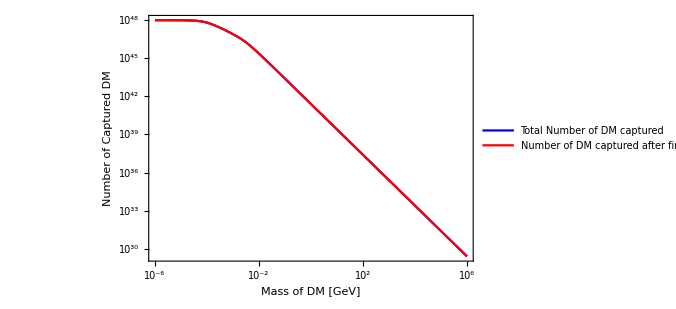

```mathematica
LogPlot[{Ctotalnew[10^x,10^-46],t*CNNboosted[1,10^x,10^-46]},{x,-6,6},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR EARTH WTH ELECTRON*)
```

```mathematica
R=6400*10^3;(*in m*)
```

```mathematica
vesc=11.2*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
vtilde=250*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=1.5 10^17(*Age in sec*);
n=10^34;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn;
```

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/Factorial[N]*NIntegrate[y *Exp[-y *tau[sigma]]*(y* tau[sigma])^N,{y,0,1}];
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12]
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^2,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{-6,"10^-6"},{-2,"10^-2"},{2,"10^2"},{6,"10^6"}},None}};
```

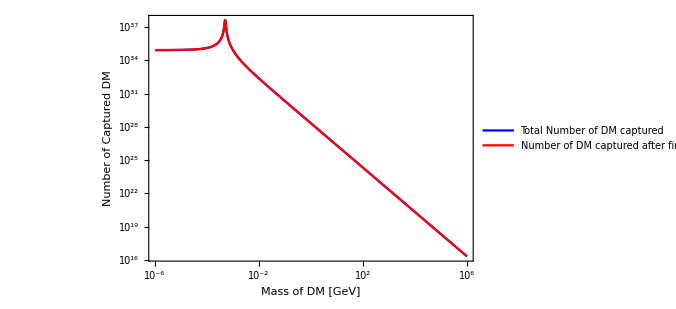

```mathematica
LogPlot[{Ctotalnew[10^x,10^-46],t*CNNboosted[1,10^x,10^-46]},{x,-6,6},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

```mathematica
(*FOR NEUTRON STAR WITH NUCLEI*)
```

```mathematica
R=10^4;(*in m*)
```

```mathematica
vesc=10^5*10^3;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
(*vtilde=247*10^3(*in m/sec*);*)
```

```mathematica
ρx=10^6*10^4;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=0.9;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=5*10^44;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

1.5×10^-49

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
(*η=((3*vtilde^2)/(2*vbar^2))^0.5;*)
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2](**Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) *);
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12];
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
T=10^4;(*in K*)
```

```mathematica
σ0=5.67*10^-8*6.24*10^9;(*in GeV/Sec*)
```

```mathematica
rhs=4*π*σ0*R^2*T^4
```

4.44608×10^27

```mathematica
myticks2={{{{-46,"10^-42"},{-48,"10^-44"},{-50,"10^-46"},{-52,"10^-48"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

```mathematica
Rasterize[ContourPlot[{10^x*Ctotalnew[10^x,10^y]==rhs,10^x*CNNboosted[1,10^x,10^y]==rhs,y==Log10[sigmaSat]},{x,0,8},{y,-46,-52},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks2,ContourStyle->{{Thick,Red},{Dashed,Blue},Black},PlotLabel->"Scattering against Nuclei in Neutron Star",PlotLegends->Placed[{"Multiple Scattering","Single Scattering"},{0.20,0.90}],FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ_p [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]]
```

-Graphics-

```mathematica
(*BRAMANTE*)
```

```mathematica
R=10^4;(*in m*)
G=6.67*10^-11;
M=1.5*2*10^30;(*in kg*)
```

```mathematica
vesc=((2*G*M)/R)^0.5;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=M/(4/3*π*R^3*1.6725*10^-27);(*in m^-3*)
```

4.2822×10^44

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

1.75144×10^-49

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= Min[1,δp[mx]/pf]*π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12];
```

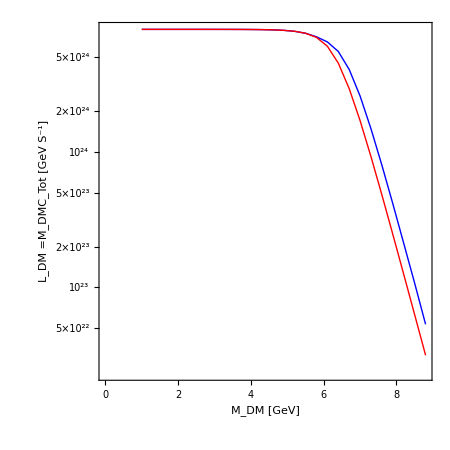

```mathematica
(*Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];*)

Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=NSum[CNNboosted[i,mx,sigma],{i,1,3}];


(*myticks={{{{10^26,"10^26"},{10^24,"10^24"},{10^22,"10^22"},{10^20,"10^20"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"}},None}};*)

ListLogPlot[{Table[{x,10^x*Ctotalnew[10^x,10^-48]},{x,1,9,0.3}],Table[{x,10^x*CNNboosted[1,10^x,10^-48]},{x,1,9,0.3}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DMC_Tot\ [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman" ]},AspectRatio->1,ImageSize->450]
```

```mathematica
(*FOR WHITE DWARF WITH ELECTRON*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

1.07143×10^-43

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= Min[1,δp[mx]/pf]*π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12];
```

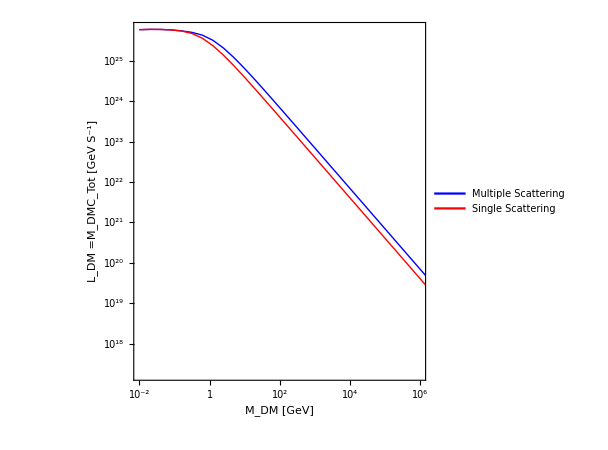

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];

Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];


myticks={{{{10^26,"10^26"},{10^24,"10^24"},{10^22,"10^22"},{10^20,"10^20"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"}},None}};

ListLogPlot[{Table[{x,10^x*Ctotalnew[10^x,10^-43]},{x,-2,8,0.3}],Table[{x,10^x*CNNboosted[1,10^x,10^-43]},{x,-2,8,0.3}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->{{-2,6},Automatic},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotLegends->Placed[{Style["Multiple Scattering",FontSize->20],Style["Single Scattering",FontSize->20]},{0.30,0.30}],AxesOrigin->{-2,Automatic},FrameTicks->myticks,FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DMC_Tot\ [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman" ]},AspectRatio->1,ImageSize->450]
```

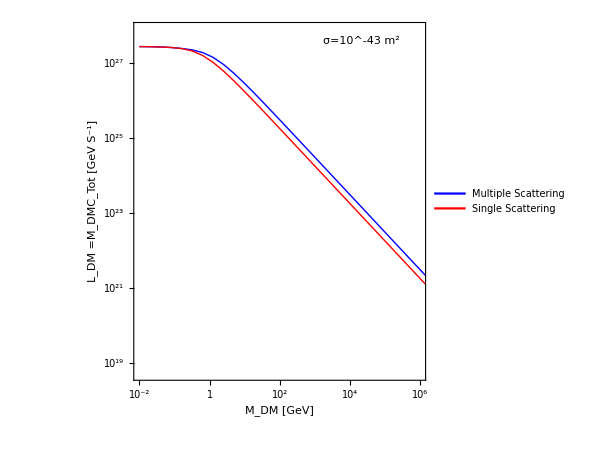

```mathematica
rlist=10^Subdivide[-2,6,27];
lum={};
lumsingle={};
Do[
p=rlist[[i]];
AppendTo[lum,p*Ctotalnew[p,10^-43]];
AppendTo[lumsingle,p*CNNboosted[1,p,10^-43]];
,{i,Length[rlist]}]

Ldm=Table[{rlist[[i]]//N,lum[[i]]},{i,Length[rlist]}];
Ldmsingle=Table[{rlist[[i]]//N,lumsingle[[i]]},{i,Length[rlist]}];
```

```mathematica
Export["WD_ELECTRON_LTOT.csv",Ldm];
Export["WD_ELECTRON_Lsingle.csv",Ldmsingle];
```

```mathematica
(*myticks2={{{{-42,"10^-38"},{-46,"10^-42"},{-50,"10^-46"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"}},None}};*)
```

```mathematica
(*ContourPlot[{10^x*Ctotalnew[10^x,10^y]==10^30,10^x*CNNboosted[1,10^x,10^y]==10^30,y==Log10[sigmaSat]},{x,-2,4},{y,-42,-50},Frame->True,FrameTicks->myticks2,PlotLabel->"Scattering against electron in White Dwarf for L= 10^28 GeV/Sec ",FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Red},{Dashed,Blue},Black},PlotLegends->Placed[{"Multiple Scattering","Single Scattering"},{0.70,0.40}],FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]*)
```

```mathematica
(*FOR WHITE DWARF WITH CARBON*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_?NumericQ,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
mphi=1000;
c=3*10^8;(*in m/s*)

g1[u_?NumericQ,mx_?NumericQ]:=(mphi^2*(1-1/βplus[mx]*u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

1.07143×10^-43

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= Min[1,δp[mx]/pf]*π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12,AccuracyGoal->5];
```

```mathematica
a[mx_?NumericQ,sigma_?NumericQ]:= Min[1,δp[mx]/pf]*π *R^2*Min[sigma/sigmaSat,1]*NIntegrate[g1[u,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,0,(vesc*βplus[mx]^0.5)/(1-βplus[mx])^0.5},MaxRecursion->12,AccuracyGoal->5];
```

```mathematica
(*Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];

Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];*)
```

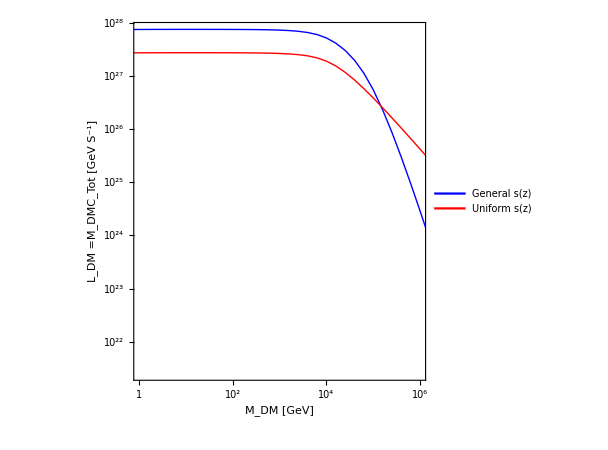

```mathematica
myticks={{{{10^28,"10^28"},{10^22,"10^22"},{10^16,"10^16"}},None},{{{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"}},None}};

ListLogPlot[{Table[{x,10^x*a[10^x,10^-43]},{x,-1,7,0.2}],Table[{x,10^x*CNNboosted[1,10^x,10^-43]},{x,-1,7,0.2}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->{{0,6},Automatic},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotLegends->Placed[{Style["General s(z)",FontSize->20],Style["Uniform s(z)",FontSize->20]},{0.30,0.30}],AxesOrigin->{0,Automatic},FrameTicks->myticks,FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DMC_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]
```

```mathematica
(*ROUGH*)
```

```mathematica
g1[u_]:=(mphi^2*(1-1/β*u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/β*(u/c)^2);
```

```mathematica
Solve[g1[u]==0,u]
```

{{u→-(vesc √β)/(√(1-β))},{u→(vesc √β)/(√(1-β))}}

```mathematica
Solve[g1[u]==1,u]
```

{{u→0},{u→0},{u→-(√(-c^2 mphi^2-mx^2 vesc^2))/mx},{u→(√(-c^2 mphi^2-mx^2 vesc^2))/mx}}

```mathematica
rlist=10^Subdivide[0,6,30];
lum={};
lumsingle={};
Do[
p=rlist[[i]];
AppendTo[lum,p*Ctotalnew[p,10^-43]];
AppendTo[lumsingle,p*CNNboosted[1,p,10^-43]];
,{i,Length[rlist]}]

Ldm=Table[{rlist[[i]]//N,lum[[i]]},{i,Length[rlist]}];
Ldmsingle=Table[{rlist[[i]]//N,lumsingle[[i]]},{i,Length[rlist]}];
Export["WD_Carbon_LTOT.csv",Ldm];
Export["WD_Carbon_Lsingle.csv",Ldmsingle];
```

```mathematica
ListLogLogPlot[Table[{rlist[[i]],lum[[i]]},{i,Length[rlist]}],PlotRange->All,Joined->True,PlotStyle->Blue,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->450];
```

```mathematica
ListLogLogPlot[Table[{rlist[[i]],lumsingle[[i]]},{i,Length[rlist]}],PlotRange->All,Joined->True,PlotStyle->Red,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->450];
```

```mathematica
(*FOR WHITE DWARF WITH NUCLEI*)
```

```mathematica
R=9*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

8.33333×10^-44

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12];
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];

Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

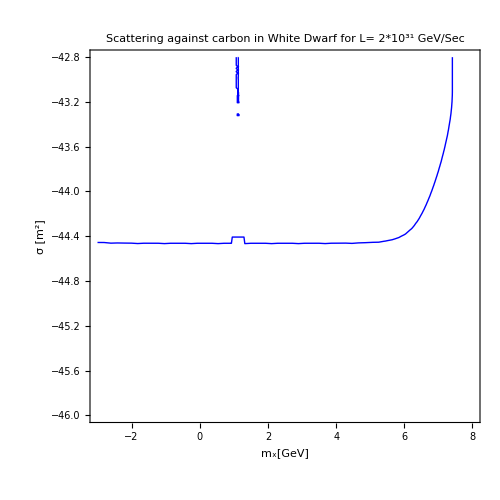

```mathematica
q=ContourPlot[{10^x*CNNboosted[1,10^x,10^y]==2.5*10^31},{x,-3,8},{y,-42.8,-46},Frame->True,PlotLabel->"Scattering against carbon in White Dwarf for L= 2*10^31 GeV/Sec ",FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue}},FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

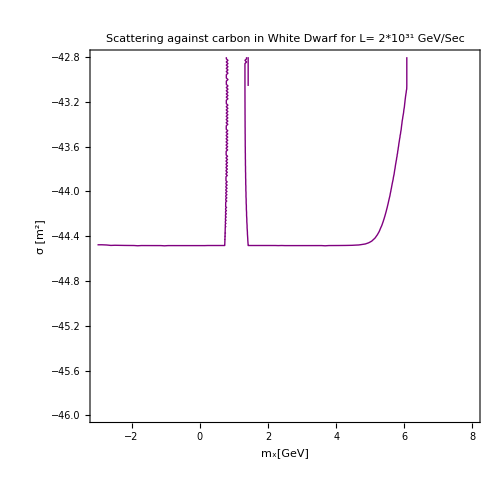

```mathematica
r=ContourPlot[{10^x*a[10^x,10^y]==2.5*10^31},{x,-3,8},{y,-42.8,-46},Frame->True,PlotLabel->"Scattering against carbon in White Dwarf for L= 2*10^31 GeV/Sec ",FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Purple}},FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

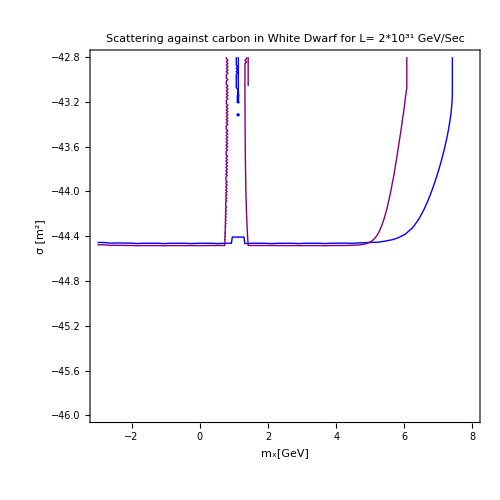

```mathematica
Show[q,r]
```

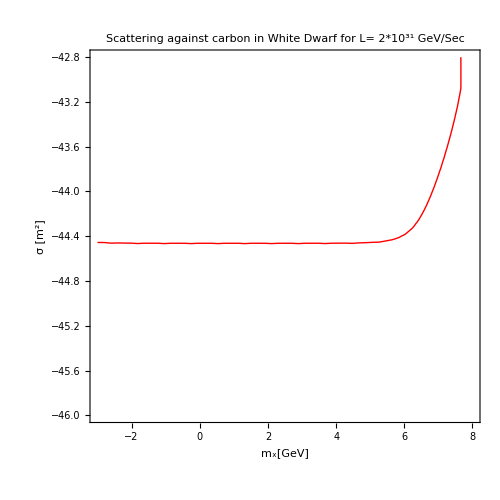

```mathematica
p=ContourPlot[{10^x*Ctotalnew[10^x,10^y]==2.5*10^31},{x,-3,8},{y,-42.8,-46},Frame->True,PlotLabel->"Scattering against carbon in White Dwarf for L= 2*10^31 GeV/Sec ",FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Red}},FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

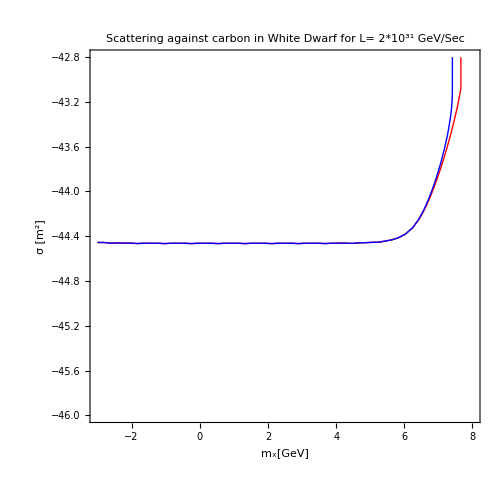

```mathematica
Show[p,q]

points=Catenate@Cases[Normal@p,Line[pts_]->pts,Infinity];
Export["fig6multi.csv",points,"Table"];


points2=Catenate@Cases[Normal@q,Line[pts_]->pts,Infinity];
Export["fig6single.csv",points2,"Table"];
```

```mathematica
(*NOW CONSIDER MASSLESS MEDIATOR AND WE WILL FOCUS ON ELECTRON SCATTERING *)
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR SUN  WITH ELECTRON*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=300*10^3;(*in m/sec*)
```

```mathematica
vtilde=250*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5;(*in GeV/m^3*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=1.5 10^17(*Age  in sec*);
n=10^34;(*in m^-3*)
```

```mathematica
δ=10^-3;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1+1/(δ*(1-δ)^(N-1)))/((1-δ*βplus[mx])^(N-1)*(1-βplus[mx]+1/(δ*(1-δ)^(N-1))))-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/((1-βplus[mx])*(1-δ*βplus[mx])^(N-1))-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=δ*(1-δ)^(N-1)*(vesc^2-(u^2+vesc^2)*(1-βplus[mx])*(1-δ*βplus[mx])^(N-1))/((u^2+vesc^2)*(1-δ*βplus[mx])^(N-1)-vesc^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn;
```

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12]
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*NSum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{-6,"10^-6"},{-2,"10^-2"},{2,"10^2"},{6,"10^6"}},None}};
```

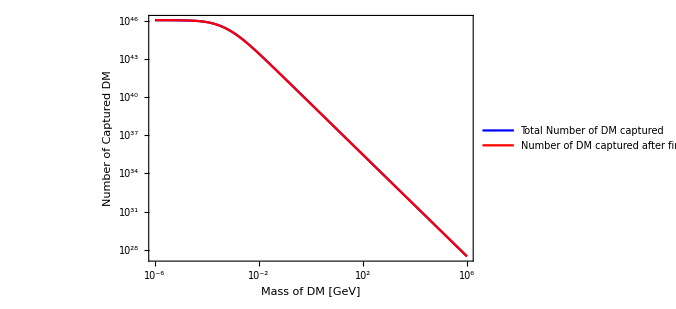

```mathematica
LogPlot[{Ctotalnew[10^x,10^-46],t*CNNboosted[1,10^x,10^-46]},{x,-6,6},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

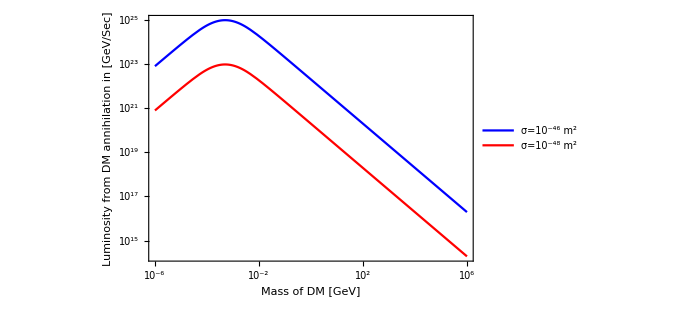

```mathematica
LogPlot[{10^x/t*Ctotalnew[10^x,10^-46],10^x/t*Ctotalnew[10^x,10^-48]},{x,-6,6},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->15,Bold],Style["Luminosity from DM annihilation in [GeV/Sec]",FontSize->15,Bold]},PlotLegends->{"σ=10^-46 m^2","σ=10^-48 m^2"},ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR NEUTRON STAR WITH ELECTRON*)
```

```mathematica
R=10^4;(*in m*)
```

```mathematica
vesc=10^5*10^3;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
vtilde=247*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5*10^4;(*in GeV/m^3*)(*Due to overdensity*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^44;(*in m^-3*)
```

```mathematica
δ=10^-3;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1+1/(δ*(1-δ)^(N-1)))/((1-δ*βplus[mx])^(N-1)*(1-βplus[mx]+1/(δ*(1-δ)^(N-1))))-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/((1-βplus[mx])*(1-δ*βplus[mx])^(N-1))-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=δ*(1-δ)^(N-1)*(vesc^2-(u^2+vesc^2)*(1-βplus[mx])*(1-δ*βplus[mx])^(N-1))/((u^2+vesc^2)*(1-δ*βplus[mx])^(N-1)-vesc^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

7.5×10^-49

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->20,WorkingPrecision->10];
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*Sum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
```

```mathematica
myticks={{Automatic,None},{{{-2,"10^-2"},{2,"10^2"},{4,"10^4"},{6,"10^6"}},None}};
```

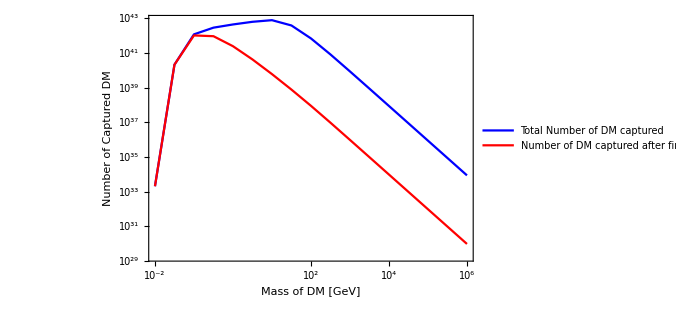

```mathematica
ListLogPlot[{Table[{x,Ctotalnew[10^x,10^-46]},{x,-2,6,0.5}],Table[{x,t*CNNboosted[1,10^x,10^-46]},{x,-2,6,0.5}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

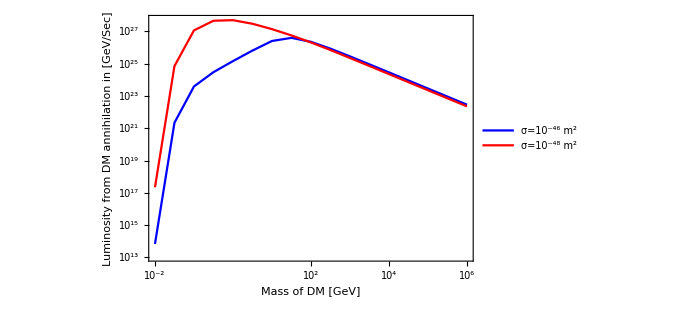

```mathematica
ListLogPlot[{Table[{x,10^x/t*Ctotalnew[10^x,10^-46]},{x,-2,6,0.5}],Table[{x,10^x/t*Ctotalnew[10^x,10^-48]},{x,-2,6,0.5}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,PlotLegends->{"σ=10^-46 m^2","σ=10^-48 m^2"},FrameLabel->{Style["Mass of DM [GeV]",FontSize->15,Bold],Style["Luminosity from DM annihilation in [GeV/Sec]",FontSize->15,Bold]},ImageSize->500]
```

```mathematica
(*CALCULATION OF N_MAX*)
(*FOR WHITE DWARF WITH ELECTRON*)
```

```mathematica
R=0.01*6.95*10^8;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
(*vtilde=247*10^3(*in m/sec*);*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
δ=10^-3;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1+1/(δ*(1-δ)^(N-1)))/((1-δ*βplus[mx])^(N-1)*(1-βplus[mx]+1/(δ*(1-δ)^(N-1))))-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/((1-βplus[mx])*(1-δ*βplus[mx])^(N-1))-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=δ*(1-δ)^(N-1)*(vesc^2-(u^2+vesc^2)*(1-βplus[mx])*(1-δ*βplus[mx])^(N-1))/((u^2+vesc^2)*(1-δ*βplus[mx])^(N-1)-vesc^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn
```

1.07914×10^-43

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->20,WorkingPrecision->10];
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=t*Sum[CNNboosted[i,mx,sigma],{i,1,Nmax[mx,sigma]}];
1/t*Ctotalnew[10^6,10^-46]
```

1.86051×10^14

```mathematica
myticks={{Automatic,None},{{{-6,"10^-6"},{-2,"10^-2"},{2,"10^2"},{6,"10^6"}},None}};
```

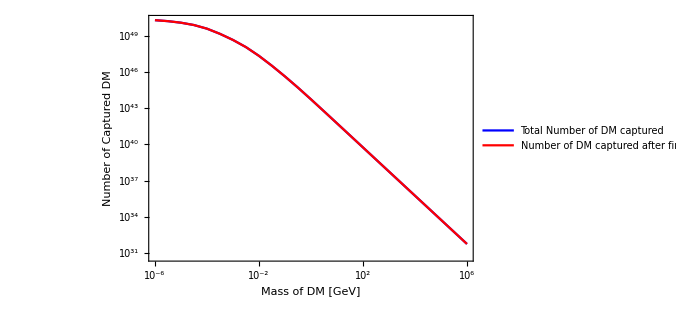

```mathematica
ListLogPlot[{Table[{x,Ctotalnew[10^x,10^-46]},{x,-6,6,0.5}],Table[{x,t*CNNboosted[1,10^x,10^-46]},{x,-6,6,0.5}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{" Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500]
```

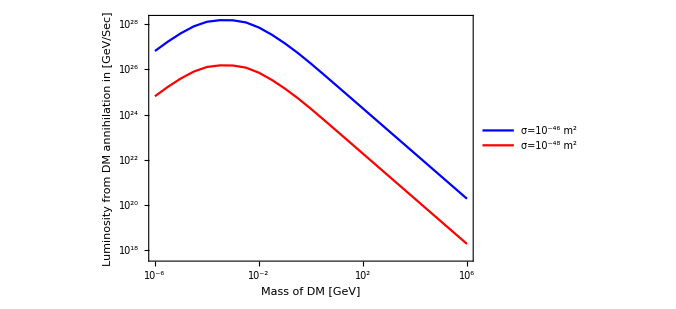

```mathematica
ListLogPlot[{Table[{x,10^x/t*Ctotalnew[10^x,10^-46]},{x,-6,6,0.5}],Table[{x,10^x/t*Ctotalnew[10^x,10^-48]},{x,-6,6,0.5}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,PlotLegends->{"σ=10^-46 m^2","σ=10^-48 m^2"},FrameLabel->{Style["Mass of DM [GeV]",FontSize->15,Bold],Style["Luminosity from DM annihilation in [GeV/Sec]",FontSize->15,Bold]},ImageSize->500]
```

```mathematica
(*FOR WHITE DWARF WITH ELECTRON MASSLESS MEDIATOR*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
```

```mathematica
Rsun=6.95 10^8(*in m*);
Msun=2 10^30(*in kg*);
Mch=1.4 *Msun;
μe=2;
Rwd[M_]:=0.0126*Rsun *(2/μe)^(5/3)*(M/Msun)^(-1/3)*(1-(M/Mch)^(4/3))^(1/2);(*in m*)
```

```mathematica
vesc[M_]:=((2*G*M)/Rwd[M])^0.5;(*in m/sec*)

vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
vtilde=247*10^3(*in m/sec*);
```

```mathematica
ρx=3*10^5*10^4;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n[M_]:=M/(mn*4/3*π*Rwd[M]^3*1.78*10^-27);(*in m^-3*)
δ=10^-3;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[M_,N_?NumericQ,mx_?NumericQ]:=vesc[M] *√((1+1/(δ*(1-δ)^(N-1)))/((1-δ*βplus[mx])^(N-1)*(1-βplus[mx]+1/(δ*(1-δ)^(N-1))))-1);
```

```mathematica
umax[M_,N_?NumericQ,mx_?NumericQ]:=vesc[M] *√(1/((1-βplus[mx])*(1-δ*βplus[mx])^(N-1))-1);
```

```mathematica
gN[M_,u_,N_?NumericQ,mx_?NumericQ]:=δ*(1-δ)^(N-1)*(vesc[M]^2-(u^2+vesc[M]^2)*(1-βplus[mx])*(1-δ*βplus[mx])^(N-1))/((u^2+vesc[M]^2)*(1-δ*βplus[mx])^(N-1)-vesc[M]^2);
```

```mathematica
Nn[M_]:=4/3*π *Rwd[M]^3*n[M];
```

```mathematica
sigmaSat[M_]:=(π *Rwd[M]^2)/Nn[M];
```

```mathematica
tau[M_,sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat[M]);
```

```mathematica
pn[M_,N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[M,sigma]*tau[M,sigma])*(Gamma[N+2]-Gamma[(N+2),tau[M,sigma]]);
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[M_?NumericQ,N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *Rwd[M]^2*pn[M,N,sigma]*NIntegrate[gN[M,u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc[M]^2),{u,umin[M,N,mx],umax[M,N,mx]},MaxRecursion->20,WorkingPrecision->10];
```

```mathematica
Nmax[M_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:=For[i=1,i≤ 10^5,i++,If[t* CNNboosted[M,i,mx,sigma]≤1,Return[i-1];Break[]]];
```

```mathematica
Ctotalnew[M_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:=Sum[CNNboosted[M,i,mx,sigma],{i,1,Nmax[M,mx,sigma]}];
```

```mathematica
Luminosity[M_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:=mx*Ctotalnew[M,mx,sigma];
```

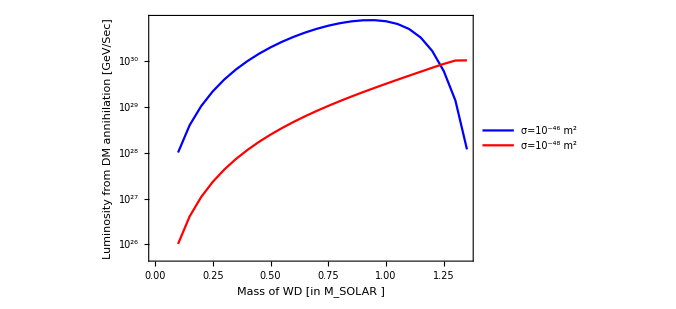

```mathematica
ListLogPlot[{Table[{y,Luminosity[y*Msun,10^-4,10^-46]},{y,0.1,1.35,0.05}],Table[{y,Luminosity[y*Msun,10^-4,10^-48]},{y,0.1,1.35,0.05}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["Mass of WD [in M_SOLAR ]",FontSize->15,Bold],Style["Luminosity from DM annihilation [GeV/Sec]",FontSize->15,Bold]},PlotLegends->{"σ=10^-46 m^2","σ=10^-48 m^2"},ImageSize->500]
```

```mathematica
(*Check*)
```

```mathematica
kb=1.38*10^-23;
T=10^7;
vcarbon=((3*kb*T)/(12*1.78*10^-27))^0.5/1000
```

139.219

```mathematica
vxmax=((3*kb*T)/(10^0*1.78*10^-27))^0.5/1000
```

482.27

```mathematica
vxmin=((3*kb*T)/(10^8*1.78*10^-27))^0.5/1000
```

0.048227

```mathematica
mevap=(3*kb*T)/((6*10^6)^2)*5.62*10^26*1000(*in MeV*)
```

6.463

```mathematica
fMBboosted[u_,mx_]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
Integrate[fMBboosted[u,mx]*u,{u,0,∞}]//FullSimplify
```

ConditionalExpression[(ⅇ^(-η^2) ρx (2 η+ⅇ^(η^2) √π (1+2 η^2) Erf[η]))/(mx √(6 π) √(1/vbar^2) η),Re[vbar^2]>0]

```mathematica
Integrate[fMBboosted[u,mx]*u^-1,{u,0,∞}]//FullSimplify
```

ConditionalExpression[(√(3/2) √(1/vbar^2) ρx Erf[η])/(mx η),Re[vbar^2]>0]

```mathematica
(*FOR WHITE DWARF WITH NUCLEI*)
```

```mathematica
R=9*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
```

```mathematica
βplus[mx_]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_,mx_]:=vesc *((N-1)/2)^0.5*βplus[mx];
```

```mathematica
umax[N_,mx_]:=vesc *((N+1)/2)^0.5*βplus[mx];
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

8.33333×10^-44

```mathematica
tau[sigma_]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_,sigma_]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_,mx_]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNbosted[N_,mx_,sigma_]:=π*R^2*pn[N,sigma]*ρx/mx*1/((1/3*vbar^2)^0.5)*(((0.5*vesc^2)/βplus[mx]^N*Log[1/(1-βplus[mx])]^(N-1)*(Exp[(-0.5*umin[N,mx]^2)/(1/3*vbar^2)]-Exp[(-0.5*umax[N,mx]^2)/(1/3*vbar^2)]))-(1/βplus[mx]-1)*(1/3*vbar^2+0.5*vesc^2+0.5*umin[N,mx]^2)*Exp[(-0.5*umin[N,mx]^2)/(1/3*vbar^2)]+(1/βplus[mx]-1)*(1/3*vbar^2+0.5*vesc^2+0.5*umax[N,mx]^2)*Exp[(-0.5*umax[N,mx]^2)/(1/3*vbar^2)])
```